## Main analysis

```mathematica
realklpt[k_,l_,a_,b_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,a,0],l==0},{(√2)*ComplexExpand[Im[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l<0}}]
```

```mathematica
Clear[η,t,ϕ,ϕ1,ϕ2,ϕ3, η1, η2, η3,We]
```

```mathematica
Clear[ohn,rho1,rho2,mu1,mu2]
```

```mathematica
Clear[η,t,ϕ1,ϕ11,ϕ12,ϕ13,ϕ2,ϕ21,ϕ22,ϕ23, η1, η2, η3]
ϕ1[a_,b_,c_,d_]:=e*ϕ11[a,b,c,d]+e^2*ϕ12[a,b,c,d]+e^3*ϕ13[a,b,c,d];
ϕ2[a_,b_,c_,d_]:=e*ϕ21[a,b,c,d]+e^2*ϕ22[a,b,c,d]+e^3*ϕ23[a,b,c,d];
η[a_,b_,c_]:=e* η1[a,b,c]+e^2* η2[a,b,c]+e^3* η3[a,b,c];
```

```mathematica
kinematicst=η[θ,φ,t]+Grad[ϕ2[r,θ,φ,t],{r,θ,φ},"Spherical"].Grad[η[θ,φ,t],{r,θ,φ},"Spherical"]-D[ϕ2[r,θ,φ,t],r]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+1/r^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ21^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ22^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ23^(0,0,1,0)[r,θ,φ,t])+1/r^2(e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ21^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ22^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ23^(0,1,0,0)[r,θ,φ,t])-e ϕ21^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ22^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ23^(1,0,0,0)[r,θ,φ,t]

```mathematica
nhat={1,-e/r D[η[θ,φ,t],θ],-e/(r*Sin[θ])D[η[θ,φ,t],φ]}/(√(1+(-e/r D[η[θ,φ,t],θ])^2+(e/(r*Sin[θ])D[η[θ,φ,t],φ])^2));
```

```mathematica
nopen=(Grad[ϕ2[r,θ,φ,t],{r,θ,φ},"Spherical"]-Grad[ϕ1[r,θ,φ,t],{r,θ,φ},"Spherical"]).nhat
```

-((e Csc[θ] (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (-1/r Csc[θ] (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t])+1/r Csc[θ] (e ϕ21^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ22^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ23^(0,0,1,0)[r,θ,φ,t])))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2)))-(e (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (-(e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t])/r+(e ϕ21^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ22^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ23^(0,1,0,0)[r,θ,φ,t])/r))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))+(-e ϕ11^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]+e ϕ21^(1,0,0,0)[r,θ,φ,t]+e^2 ϕ22^(1,0,0,0)[r,θ,φ,t]+e^3 ϕ23^(1,0,0,0)[r,θ,φ,t])/(√(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))

```mathematica
curvature=2/r+(-Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t]-Cot[θ] Derivative[1,0,0][η][θ,φ,t]-Derivative[2,0,0][η][θ,φ,t])/r^2+1/r^4(Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t] (Derivative[1,0,0][η][θ,φ,t])^2+Cot[θ] (Derivative[1,0,0][η][θ,φ,t])^3+2 Csc[θ]^2 Derivative[0,1,0][η][θ,φ,t] Derivative[1,0,0][η][θ,φ,t] Derivative[1,1,0][η][θ,φ,t]+3 (Derivative[1,0,0][η][θ,φ,t])^2 Derivative[2,0,0][η][θ,φ,t]);
```

```mathematica
(*Clear[rho1,rho2,We];*)
normalst=(-rho1*(D[ϕ1[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ1[r,θ,φ,t],φ]^2)/r^2+D[ϕ1[r,θ,φ,t],θ]^2/r^2+D[ϕ1[r,θ,φ,t],r]^2))+rho2*(D[ϕ2[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ2[r,θ,φ,t],φ]^2)/r^2+D[ϕ2[r,θ,φ,t],θ]^2/r^2+D[ϕ2[r,θ,φ,t],r]^2)))-1/We*(curvature);(*e*(1+η[θ,φ,t])*Cos[θ]*Sin[t]*)
```

```mathematica
kinematicstpertr1=Series[kinematicst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (η1[θ,φ,t]-ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ21^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ21^(0,1,0,0)[1,θ,φ,t]-ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ21^(0,1,0,0)[1,θ,φ,t]-ϕ23^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ21^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

```mathematica
nopenstpertr1=Series[nopen/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (-ϕ11^(1,0,0,0)[1,θ,φ,t]+ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (-ϕ12^(1,0,0,0)[1,θ,φ,t]+ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

```mathematica
normalstpertr1=Series[normalst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

-2/We+e ((2 η1[θ,φ,t]+Csc[θ]^2 η1^(0,2,0)[θ,φ,t]+Cot[θ] η1^(1,0,0)[θ,φ,t]+η1^(2,0,0)[θ,φ,t])/We-rho1 ϕ11^(0,0,0,1)[1,θ,φ,t]+rho2 ϕ21^(0,0,0,1)[1,θ,φ,t])+e^2 (1/We(-2 (η1[θ,φ,t]^2-η2[θ,φ,t])+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])-1/2 rho1 (2 ϕ12^(0,0,0,1)[1,θ,φ,t]+Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])+rho2 (ϕ22^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]))+e^3 (1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+rho1 (-ϕ13^(0,0,0,1)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))-2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])+rho2 (ϕ23^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))+2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])+2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t]))

```mathematica
wem
```

40

```mathematica
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem))
```

(√((k (1+k) (-2+k+k^2))/((1+k) ρ1+k ρ2)))/(2 √10)

```mathematica
magkl1mn2[0,0,1,0,1,2,0,3]//N
```

4.24642

```mathematica
DSolve[x''[t]+2*dk*x'[t]+zt^2*x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(t (-dk-√(dk^2-zt^2))) C[1]+ⅇ^(t (-dk+√(dk^2-zt^2))) C[2]}}

```mathematica
magkl1mn2[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_]:=(
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);delta=oh/wem;ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;

qkl=Integrate[Cos[θ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k);
magkl=(2nk*Abs[qkl])/(√((1-ζk^2)^2+4*Δk^2))
)
```

```mathematica
psikl1mn2[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_]:=(Clear[tt,wem,psi];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);delta=oh/wem;ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;

qkl=Integrate[Cos[θ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k);

d1=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Cos[tt]];
d2=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Sin[tt]];
psi=ArcTan[d2,-d1])
```

```mathematica
magkl1mn2[0,0,1,0,1,4,0,3]*Sin[s-psikl1mn2[0,0,1,0,1,4,0,3]]//N
```

-0.886227 Sin[s]

Once everything is loaded for the first time, run from here .

```mathematica
ohn=0.043;rho1=0.86;rho2=0.14;mu1=0.71;mu2=0.29;(*rolling drop*)
```

```mathematica
ohn=0.026;rho1=0.4;rho2=1;mu1=0.0;mu2=1;(*bubble limit*)
```

```mathematica
ohn=0.034;rho1=0.86;rho2=1-rho1;mu1=0.71;mu2=1-mu1;
```

```mathematica
b401p2[s]
```

-0.886227 Sin[3.14159-s]

```mathematica
b201p2[s_]:=(wem=(2(2+1)(2^2+2-2))/(rho1*(2+1)+rho2*2);ζk=√((2(2+1)(2^2+2-2))/((rho1*(2+1)+rho2*2)wem));
b201amp=c20*Cos[ζk*s]+d20*Sin[ζk*s])
```

```mathematica
b201p2[s]
```

c20 Cos[1. s]+d20 Sin[1. s]

```mathematica
b211p2[s_]:=c21*Cos[s]+d21*Sin[s];
```

```mathematica
b301p2[s_]:=(wem=(3(3+1)(3^2+3-3))/(rho1*(3+1)+rho2*3);ζ3=√((3(3+1)(3^2+3-3))/((rho1*(3+1)+rho2*3)wem));
b201amp=c30*Cos[ζ3*s]+d30*Sin[ζ3*s])
```

```mathematica
etaa1p2[a_,b_,c_]:=b201p2[c]*realklpt[2,0,a,b]+b211p2[c]*realklpt[2,1,a,b](*+b301p2[c]*realklpt[3,0,a,b]*)
```

```mathematica
fi1o[rr_,a_,b_,c_]:=-D[b201p2[c],c]/(3 rr^3)*realklpt[2,0,a,b]-D[b211p2[c],c]/(3 rr^3)*realklpt[2,1,a,b](*-D[b301p2[c],c]/(4 rr^5)*realklpt[3,0,a,b]*)
```

```mathematica
fi1i[rr_,a_,b_,c_]:=D[b201p2[c],c]/2*rr^2*realklpt[2,0,a,b]+D[b211p2[c],c]/2 rr^2*realklpt[2,1,a,b](*+D[b301p2[c],c]/3*rr^3*realklpt[3,0,a,b]*)
```

```mathematica
fi1o[r,a,b,c]
```

-(√(5/π) (-1+3 Cos[a]^2) (1. d20 Cos[1. c]-1. c20 Sin[1. c]))/(12 r^3)+(√(5/(3 π)) Cos[a] Cos[b] Sin[a] (d21 Cos[c]-c21 Sin[c]))/(2 r^3)-(√(7/π) (-3 Cos[a]+5 Cos[a]^3) (1. d31 Cos[1. c]-1. c31 Sin[1. c]))/(16 r^5)

```mathematica
Coefficient[kinematicstpertr1,e^2]
```

η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ21^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ21^(0,1,0,0)[1,θ,φ,t]-ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]

```mathematica
kkl1funp2=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ21][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1p2[θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi1o[r,θ,φ,t]]}
```

(1/2 √(5/(3 π)) Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t])+1/2 √(5/π) Cos[θ] (d20 Cos[t]-c20 Sin[t]) Sin[θ]) (-1/2 √(15/π) Cos[2 θ] Cos[φ] (c21 Cos[t]+d21 Sin[t])-3/2 √(5/π) Cos[θ] (c20 Cos[t]+d20 Sin[t]) Sin[θ])-(1/4 √(5/π) (-1+3 Cos[θ]^2) (c20 Cos[t]+d20 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) (-√(5/π) (-1+3 Cos[θ]^2) (d20 Cos[t]-c20 Sin[t])+√(15/π) Cos[φ] (d21 Cos[t]-c21 Sin[t]) Sin[2 θ])-(5 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t]) (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]^2 Sin[φ]^2)/(16 π)

```mathematica
expr=kkl1funp2;
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c20,d20,c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];

(*rules is a list of {exponent vector}->coefficient(θ,φ,t) e.g.,{2,0,0,0}->f(θ,φ,t) means c31^2*f(θ,φ,t)*)

(*Now integrate each coefficient over θ and φ*)
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,0,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
k201ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],We->40}//N
```

-0.540671 c20^2 Cos[t] Sin[t]-0.270336 c21^2 Cos[t] Sin[t]+(0.540671 d20^2+0.270336 d21^2) Cos[t] Sin[t]+c20 d20 (0.540671 Cos[t]^2-0.540671 Sin[t]^2)+c21 d21 (0.270336 Cos[t]^2-0.270336 Sin[t]^2)

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
k211ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],We->40}//N
```

d21 (0.270336 c20 Cos[t]^2+0.540671 d20 Cos[t] Sin[t]-0.270336 c20 Sin[t]^2)+c21 (0.270336 d20 Cos[t]^2-0.540671 c20 Cos[t] Sin[t]-0.270336 d20 Sin[t]^2)

```mathematica
Coefficient[normalstpertr1,e^2]
```

1/We(2 η2[θ,φ,t]+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]-2 (η1[θ,φ,t]^2+Csc[θ]^2 η1[θ,φ,t] η1^(0,2,0)[θ,φ,t]+Cot[θ] η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η1[θ,φ,t] η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])-1/2 rho1 (2 ϕ12^(0,0,0,1)[1,θ,φ,t]+Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])+rho2 (ϕ22^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])

```mathematica
nkl1funp2=1/We(-2 (η1[θ,φ,t]^2+Csc[θ]^2 η1[θ,φ,t] Derivative[0,2,0][η1][θ,φ,t]+Cot[θ] η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0][η1][θ,φ,t]))-1/2 rho1 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])+rho2 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1p2[θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi1o[r,θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi1i[r,θ,φ,t]]} ;
```

```mathematica
kkl1funp2-kkl1fun//FullSimplify
```

$Aborted

```mathematica
expr=nkl1funp2;
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c20,d20,c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];

(*rules is a list of {exponent vector}->coefficient(θ,φ,t) e.g.,{2,0,0,0}->f(θ,φ,t) means c31^2*f(θ,φ,t)*)

(*Now integrate each coefficient over θ and φ*)
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,0,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
n201ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],We->40}//N//FullSimplify
```

0.025 ((-6.30783 d20^2 rho1-3.15392 d21^2 rho1+c20^2 (1.80224+7.20895 rho1-7.20895 rho2)+c21^2 (0.901119+3.60448 rho1-3.60448 rho2)+4.80597 d20^2 rho2+2.40298 d21^2 rho2) Cos[t]^2+(c20 d20 (3.60448+27.0336 rho1-24.0298 rho2)+c21 d21 (1.80224+13.5168 rho1-12.0149 rho2)) Cos[t] Sin[t]+(d20^2 (1.80224+7.20895 rho1-7.20895 rho2)+d21^2 (0.901119+3.60448 rho1-3.60448 rho2)+c21^2 (-3.15392 rho1+2.40298 rho2)+c20^2 (-6.30783 rho1+4.80597 rho2)) Sin[t]^2)

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
n211ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],We->40}//N//FullSimplify
```

0.025 ((c20 c21 (1.80224+7.20895 rho1-7.20895 rho2)+d20 d21 (-6.30783 rho1+4.80597 rho2)) Cos[t]^2+(c21 d20+c20 d21) (1.80224+13.5168 rho1-12.0149 rho2) Cos[t] Sin[t]+(d20 d21 (1.80224+7.20895 rho1-7.20895 rho2)+c20 c21 (-6.30783 rho1+4.80597 rho2)) Sin[t]^2)

```mathematica
Coefficient[nopenstpertr1,e^3]
```

Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t]

```mathematica
lkl1funp2=-η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1p2[θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi1o[r,θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi1i[r,θ,φ,t]]} ;
```

```mathematica
expr=lkl1funp2;
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c20,d20,c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,0,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
l201ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],We->40}//N//FullSimplify
```

(-0.901119 c20 d20-0.450559 c21 d21) Cos[2 t]+(0.901119 c20^2+0.450559 c21^2-0.901119 d20^2-0.450559 d21^2) Cos[t] Sin[t]

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
l211ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],We->40}//N//FullSimplify
```

(-0.450559 c21 d20-0.450559 c20 d21) Cos[2 t]+(0.450559 c20 c21-0.450559 d20 d21) Sin[2 t]

```mathematica
Integrate[realklpt[2,0,t,p]*realklpt[2,1,t,p]*realklpt[2,0,t,p]*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
b202funp2[ohn,rho1,rho2,mu1,mu2,2]
```

0.0587618 c20^2+0.0293809 c21^2+0.0587618 d20^2+0.0293809 d21^2+(-0.101754 c20^2-0.0508768 c21^2-0.0159218 c20 d20+0.101754 d20^2-0.00796092 c21 d21+0.0508768 d21^2) Cos[2 t]+(0.00796092 c20^2+0.00398046 c21^2-0.203507 c20 d20-0.00796092 d20^2-0.101754 c21 d21-0.00398046 d21^2) Sin[2 t]

```mathematica
f201p2
```

0.0587618 c20^2+0.0293809 c21^2+0.0587618 d20^2+0.0293809 d21^2+0.306727 c20^2 Cos[2 t]+0.153363 c21^2 Cos[2 t]+0.0102835 c20 d20 Cos[2 t]-0.306727 d20^2 Cos[2 t]+0.00514176 c21 d21 Cos[2 t]-0.153363 d21^2 Cos[2 t]-0.952791 Sin[t]-0.00514176 c20^2 Sin[2 t]-0.00257088 c21^2 Sin[2 t]+0.613454 c20 d20 Sin[2 t]+0.00514176 d20^2 Sin[2 t]+0.306727 c21 d21 Sin[2 t]+0.00257088 d21^2 Sin[2 t]

```mathematica
Rationalize[b202funp2[ohn,rho1,rho2,mu1,mu2,2]]
```

0.0587618 c20^2+0.0293809 c21^2+0.0587618 d20^2+0.0293809 d21^2-0.0920901 c20 Cos[t]-c20 ζ1 Cos[t]+0.306727 c20^2 Cos[2 t]+0.153363 c21^2 Cos[2 t]+0.0102835 c20 d20 Cos[2 t]-0.306727 d20^2 Cos[2 t]+0.00514176 c21 d21 Cos[2 t]-0.153363 d21^2 Cos[2 t]-0.952791 Sin[t]-0.0920901 d20 Sin[t]-d20 ζ1 Sin[t]-0.00514176 c20^2 Sin[2 t]-0.00257088 c21^2 Sin[2 t]+0.613454 c20 d20 Sin[2 t]+0.00514176 d20^2 Sin[2 t]+0.306727 c21 d21 Sin[2 t]+0.00257088 d21^2 Sin[2 t]

```mathematica
b212funp2[ohn,rho1,rho2,mu1,mu2,2]
```

0.0587618 c20 c21+0.0587618 d20 d21-0.0920901 c21 Cos[t]-c21 ζ1 Cos[t]+0.306727 c20 c21 Cos[2 t]+0.060074 c20 d20 Cos[2 t]+0.00514176 c21 d20 Cos[2 t]+0.00514176 c20 d21 Cos[2 t]+0.030037 c21 d21 Cos[2 t]-0.306727 d20 d21 Cos[2 t]-0.0920901 d21 Sin[t]-d21 ζ1 Sin[t]-0.030037 c20^2 Sin[2 t]-0.00514176 c20 c21 Sin[2 t]-0.0150185 c21^2 Sin[2 t]+0.306727 c21 d20 Sin[2 t]+0.030037 d20^2 Sin[2 t]+0.306727 c20 d21 Sin[2 t]+0.00514176 d20 d21 Sin[2 t]+0.0150185 d21^2 Sin[2 t]

```mathematica
b202funp2[oh_,ρ1_,ρ2_,μ1_,μ2_,m_]:=(Clear[f1,f2,f3,f4,f5,Δk,k];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));fkk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=oh/(√wem)(μ1*(k-1)+μ2*(k+2))*fkk;
nkk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k);mk=√((2*m+1)/(4*Pi));
gkk=(ρ1*k)/(ρ1(k+1)+ρ2*k);hkk=2*oh/(√wem)*μ1*(k+2);
ff20=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi},{φ,0,2Pi}];
ff21=Integrate[(realklpt[2,1,θ,φ])*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi},{φ,0,2Pi}];
rhs202=Rationalize[TrigReduce[nkk*mk*ff20*Sin[t]-D[k201ffp2,t]-2Δk*k201ffp2+fkk*n201ffp2-gkk*D[l201ffp2,t]-hkk*l201ffp2-ζ1*b201p2[t](*-2Δk*b201p2[t]*)]]
(*f1=Integrate[(1/(2Pi))*f201p2,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f201p2*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f201p2*Sin[2t],{t,-Pi,Pi}];*)
(*
b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop*))
```

```mathematica
nkk*mk*ff20*Sin[t]
```

-0.952791 Sin[t]

```mathematica
k201ffp2
```

-0.540671 c20^2 Cos[t] Sin[t]-0.270336 c21^2 Cos[t] Sin[t]+(0.540671 d20^2+0.270336 d21^2) Cos[t] Sin[t]+c20 d20 (0.540671 Cos[t]^2-0.540671 Sin[t]^2)+c21 d21 (0.270336 Cos[t]^2-0.270336 Sin[t]^2)

```mathematica
b212funp2[ohn,rho1,rho2,mu1,mu2,2]
```

0.117524 c20 c21+0.117524 d20 d21+(-0.204485 c20 c21+0.204485 d20 d21) Cos[2 t]+(-0.204485 c21 d20-0.204485 c20 d21) Sin[2 t]

```mathematica
b212funp2[ohn,rho1,rho2,mu1,mu2,2]
```

```mathematica
Integrate[(SphericalHarmonicY[2,0,θ,φ]*realklpt[2,1,θ,φ])*Sin[θ]*realklpt[2,1,θ,φ],{θ,0,Pi},{φ,0,2Pi}]
```

(√(5/π))/14

```mathematica
Integrate[(b201p2[t]*SphericalHarmonicY[2,0,θ,φ]+b211p2[t]*realklpt[2,1,θ,φ])*mk*SphericalHarmonicY[2,0,θ,φ],{θ,0,Pi},{φ,0,2Pi}]
```

55/128 √(5 π) (c20 Cos[1. t]+d20 Sin[1. t])

```mathematica
Clear[f201p2]
```

```mathematica
b212funp2[oh_,ρ1_,ρ2_,μ1_,μ2_,m_]:=(Clear[f1,f2,f3,f4,f5,Δk,k];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));fkk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=oh/(√wem)(μ1*(k-1)+μ2*(k+2))*fkk;
nkk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k);mk=√((2*m+1)/(4*Pi));
gkk=(ρ1*k)/(ρ1(k+1)+ρ2*k);hkk=2*oh/(√wem)*μ1*(k+2);
(*t201=Integrate[(b201p2[t]*SphericalHarmonicY[2,0,θ,φ]+b211p2[t]*realklpt[2,1,θ,φ])*mk*SphericalHarmonicY[2,0,θ,φ],{θ,0,Pi},{φ,0,2Pi}];*)
f211p2=Rationalize[TrigReduce[-D[k211ffp2,t]-2Δk*k211ffp2+fkk*n211ffp2-gkk*D[l211ffp2,t]-hkk*l211ffp2-hkk*l201ffp2-ζ1*b211p2[t]-2Δk*b211p2[t]]](*;
f1=Integrate[(1/(2Pi))*f201p2,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f201p2*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f201p2*Sin[2t],{t,-Pi,Pi}];

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop*))
```

```mathematica
b202funp2[ohn,rho1,rho2,mu1,mu2,2]
```

0.0587618 c20^2+0.0293809 c21^2+0.0587618 d20^2+0.0293809 d21^2-c20 ζ1 Cos[t]+0.306727 c20^2 Cos[2 t]+0.153363 c21^2 Cos[2 t]+0.0102835 c20 d20 Cos[2 t]-0.306727 d20^2 Cos[2 t]+0.00514176 c21 d21 Cos[2 t]-0.153363 d21^2 Cos[2 t]-0.952791 Sin[t]-d20 ζ1 Sin[t]-0.00514176 c20^2 Sin[2 t]-0.00257088 c21^2 Sin[2 t]+0.613454 c20 d20 Sin[2 t]+0.00514176 d20^2 Sin[2 t]+0.306727 c21 d21 Sin[2 t]+0.00257088 d21^2 Sin[2 t]

```mathematica
fc20=Integrate[(1/Pi)*b202funp2[ohn,rho1,rho2,mu1,mu2,2]*Cos[t],{t,-Pi,Pi}]//Rationalize
```

-c20 ζ1

```mathematica
fs20=Integrate[(1/Pi)*b202funp2[ohn,rho1,rho2,mu1,mu2,2]*Sin[t],{t,-Pi,Pi}]//Rationalize
```

-0.952791-d20 ζ1

```mathematica
fc21=Integrate[(1/Pi)*b212funp2[ohn,rho1,rho2,mu1,mu2,2]*Cos[t],{t,-Pi,Pi}]//Rationalize//Chop
```

-0.31831 c21 (0.28931+3.14159 ζ1)

```mathematica
fs21=Integrate[(1/Pi)*b212funp2[ohn,rho1,rho2,mu1,mu2,2]*Sin[t],{t,-Pi,Pi}]//Rationalize//Chop
```

-0.0920901 d21-d21 ζ1

```mathematica
Solve[{fc20==0,fs20==0,fc21==0,fs21==0},{c20,d20,c21,d21}]
```

{{c20→0.,d20→0.952791/(-0.0920901-1. ζ1),c21→0.,d21→0.}}

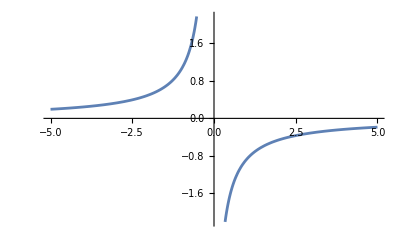

```mathematica
Plot[0.9527913020215991/(-0.09209013978789395-1. ζ1),{ ζ1,-5,5}]
```

```mathematica
b202fp2[c_]:=b202funp2[0,rho1,rho2,mu1,mu2,2]/.t->c
b212fp2[c_]:=b212funp2[0,rho1,rho2,mu1,mu2,2]/.t->c
(*b44fp2[c_]:=b402funp2[0,rho1,rho2,mu1,mu2,3]/.t->c*)
k202fp2[c_]:=k201ffp2/.t->c
k212fp2[c_]:=k211ffp2/.t->c
l202fp2[c_]:=l201ffp2/.t->c
l212fp2[c_]:=l211ffp2/.t->c
etaa2p2[a_,b_,c_]:=b202fp2[c]*realklpt[2,0,a,b]+b212fp2[c]*realklpt[2,1,a,b]
fi2o[rr_,a_,b_,c_]:=-(D[b202fp2[c],c]+2k202fp2[c])/(3 rr^3)*realklpt[2,0,a,b]-(D[b212fp2[c],c]+2k212fp2[c])/(3 rr^4)*realklpt[2,1,a,b];
fi2i[rr_,a_,b_,c_]:=(D[b202fp2[c],c]+2k202fp2[c]+2l202fp2[c])/2*rr^2*realklpt[2,0,a,b]+(D[b212fp2[c],c]+2k212fp2[c]+2l212fp2[c])/3 rr^3*realklpt[3,1,a,b]
```

```mathematica
kinematicoe3=Coefficient[kinematicstpertr1,e^3]
```

η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ21^(0,1,0,0)[1,θ,φ,t]-ϕ23^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ21^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t]

```mathematica
kkl2funp2=(-2 η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+Derivative[1,0,0][η2][θ,φ,t]) Derivative[0,1,0,0][ϕ21][1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] Derivative[0,1,0][η1][θ,φ,t]+Derivative[0,1,0][η2][θ,φ,t]) Derivative[0,0,1,0][ϕ21][1,θ,φ,t]+Derivative[0,1,0][η1][θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1p2[θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi1o[r,θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi1i[r,θ,φ,t]],
η2->Function[{θ,φ,t},etaa2p2[θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi2o[r,θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi2i[r,θ,φ,t]]} ;
```

```mathematica
expr=kkl2funp2;
exprsub=Expand[Rationalize[expr,0]](*/. {Cos[t]->ct,Sin[t]->st,Cos[2*t]->ct2,Sin[2*t]->st2}*);
params={c20,d20,c21,d21(*,ct,st,ct2,st2*)};
rulesp2=CoefficientRules[Rationalize[exprsub,0],params];

(*rules is a list of {exponent vector}->coefficient(θ,φ,t) e.g.,{2,0,0,0}->f(θ,φ,t) means c31^2*f(θ,φ,t)*)

(*Now integrate each coefficient over θ and φ*)
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,0,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rulesp2];
(*Reassemble*)
k202ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {(*ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],*)We->40}//N//Chop
```

-0.0632435 d20^3 Cos[3. t]-0.213537 c20^3 Sin[t]-0.294322 c20 c21^2 Sin[t]+0.323642 c20 d20^2 Sin[t]-0.211342 c21 d20 d21 Sin[t]+0.331563 c20 d21^2 Sin[t]+c20 (1.13682 c20^2+1.13682 c21^2) Cos[t]^2 Sin[t]-0.126487 c20^3 Cos[2. t] Sin[t]-0.207272 c20 c21^2 Cos[2. t] Sin[t]+0.379461 c20 d20^2 Cos[2. t] Sin[t]+0.414544 c21 d20 d21 Cos[2. t] Sin[t]-0.361138 c20 d21^2 Cos[2. t] Sin[t]+Cos[t] (0.528974 c20^2 d20-0.331563 c21^2 d20+0.150294 d20^3+0.779752 c20 c21 d21+0.294322 d20 d21^2+(-1.70523 c20^2 d20-0.361138 c21^2 d20-0.722277 c20 c21 d21-0.207272 d20 d21^2) Cos[2. t]+d20 (-1.13682 d20^2-1.13682 d21^2) Sin[t]^2)-0.852616 c20 d20^2 Sin[3. t]-0.568411 c21 d20 d21 Sin[3. t]+0.0948652 c20^2 d20 Csc[t] Sin[4. t]

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rulesp2];
(*Reassemble*)
k212ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {(*ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],*)We->40}//N//Chop
```

c21 (1.13682 c20^2+1.13682 c21^2) Cos[t]^2 Sin[t]+(-0.294322 c20^2 c21-0.0533843 c21^3+0.331563 c21 d20^2-0.211342 c20 d20 d21+0.294064 c21 d21^2+(-0.207272 c20^2 c21-0.0316217 c21^3-0.361138 c21 d20^2+0.414544 c20 d20 d21+0.0948652 c21 d21^2) Cos[2. t]) Sin[t]+Cos[t] (0.779752 c20 c21 d20-0.331563 c20^2 d21+0.558551 c21^2 d21-0.274088 d20^2 d21+0.0533843 d21^3+(-0.722277 c20 c21 d20-0.361138 c20^2 d21-1.61037 c21^2 d21+0.568411 d20^2 d21-0.0316217 d21^3) Cos[2. t]-1.13682 d21^3 Sin[t]^2)+d21 ((-0.568411 c20 d20-0.852616 c21 d21) Sin[3. t]-0.051818 d20^2 Csc[t] Sin[4. t])

```mathematica
nkl2funp2=1/We(2 η1[θ,φ,t]^3+3 Csc[θ]^2 η1[θ,φ,t]^2 Derivative[0,2,0][η1][θ,φ,t]+3 Cot[θ] η1[θ,φ,t]^2 Derivative[1,0,0][η1][θ,φ,t]-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]+3 η1[θ,φ,t]^2 Derivative[2,0,0][η1][θ,φ,t]-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]-2 (2 η1[θ,φ,t] η2[θ,φ,t]+Csc[θ]^2 (η2[θ,φ,t] Derivative[0,2,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[0,2,0][η2][θ,φ,t])+Cot[θ] (η2[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0][η2][θ,φ,t])+η2[θ,φ,t] Derivative[2,0,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0][η2][θ,φ,t]))+rho1 (-η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])+rho2 (η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1p2[θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi1o[r,θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi1i[r,θ,φ,t]],
η2->Function[{θ,φ,t},etaa2p2[θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi2o[r,θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi2i[r,θ,φ,t]]} ;
```

```mathematica
expr=nkl2funp2;
exprsub=Expand[Rationalize[expr,0]](*/. {Cos[t]->ct,Sin[t]->st,Cos[2*t]->ct2,Sin[2*t]->st2}*);
params={c20,d20,c31,d31(*,ct,st,ct2,st2*)};
rules=CoefficientRules[Rationalize[exprsub,0],params];

(*rules is a list of {exponent vector}->coefficient(θ,φ,t) e.g.,{2,0,0,0}->f(θ,φ,t) means c31^2*f(θ,φ,t)*)

(*Now integrate each coefficient over θ and φ*)
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,0,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
n202ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {(*ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],*)We->40}//N//Chop
```

-0.00230331 Sin[t] (77.9933 c20^2 d20+61.3973 c21^2 d20-37.6433 d20^3-64.6415 c20 c21 d21+3.33481 d20 d21^2+(-37.6433 c20^3-61.352 c21 d20 d21+c20 (1.69007 c21^2+77.9933 d20^2+63.0421 d21^2)) Cot[t]+Cos[2. t] (173.455 c20^2 d20-3.28949 c21^2 d20-57.8183 d20^3-6.57898 c20 c21 d21+3.28949 d20 d21^2+53.8183 c20^3 Cot[t]-161.455 c20 d20^2 Cot[t])+Csc[t] ((-1.64475 c20 c21^2+3.28949 c21 d20 d21+1.64475 c20 d21^2) Cos[3. t]+c20 (c20^2-3. d20^2) Csc[t] Sin[4. t]))

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
n212ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {(*ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],*)We->40}//N//Chop
```

0.025 ((0.995321 c20^2 c21-0.0155326 c21^3-5.42455 c21 d20^2+6.41987 c20 d20 d21-0.0155326 c21 d21^2) Cos[t]+(0.535212 c20^2 c21+2.62878 c21^3-0.535212 c21 d20^2-1.07042 c20 d20 d21-7.88634 c21 d21^2) Cos[3. t]+(7.49029 c20 c21 d20-4.88934 c20^2 d21+7.87081 c21^2 d21+0.46011 d20^2 d21-2.64431 d21^3+(2.14085 c20 c21 d20+1.07042 c20^2 d21+15.7727 c21^2 d21-1.07042 d20^2 d21-5.25756 d21^3) Cos[2. t]) Sin[t])

```mathematica
kinematicoe3=Coefficient[nopenstpertr1,e^3]
```

Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t]

```mathematica
lkl2funp2=Csc[θ] Derivative[0,1,0][η1][θ,φ,t] (Csc[θ] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]-Csc[θ] Derivative[0,0,1,0][ϕ21][1,θ,φ,t])+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-Derivative[0,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]+η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]+1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1p2[θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi1o[r,θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi1i[r,θ,φ,t]],
η2->Function[{θ,φ,t},etaa2p2[θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi2o[r,θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi2i[r,θ,φ,t]]} ;
```

```mathematica
expr=lkl2funp2;
exprsub=Expand[Rationalize[expr,0]](*/. {Cos[t]->ct,Sin[t]->st,Cos[2*t]->ct2,Sin[2*t]->st2}*);
params={c20,d20,c21,d21(*,ct,st,ct2,st2*)};
rules=CoefficientRules[Rationalize[exprsub,0],params];

(*rules is a list of {exponent vector}->coefficient(θ,φ,t) e.g.,{2,0,0,0}->f(θ,φ,t) means c31^2*f(θ,φ,t)*)

(*Now integrate each coefficient over θ and φ*)
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,0,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
l202ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {(*ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],*)We->40}//N//Chop
```

0.193492 c20^3 Sin[t]+0.325185 c20 c21^2 Sin[t]+0.949291 c20 d20^2 Sin[t]+0.531122 c21 d20 d21 Sin[t]+0.286477 c20 d21^2 Sin[t]+c20 (-1.70523 c20^2-1.70523 c21^2) Cos[t]^2 Sin[t]+Cos[2. t] (0.450559 c20 d20+0.22528 c21 d21+(0.0484086 c20^3+0.180101 c20 c21^2+2.41262 c20 d20^2+1.34503 c21 d20 d21+0.672515 c20 d21^2) Sin[t])+Cos[t] (-0.949291 c20^2 d20-0.286477 c21^2 d20-0.193492 d20^3-0.531122 c20 c21 d21-0.325185 d20 d21^2+(2.41262 c20^2 d20+0.672515 c21^2 d20+0.0484086 d20^3+1.34503 c20 c21 d21+0.180101 d20 d21^2) Cos[2. t]+Sin[t] (-0.450559 c20^2+0.450559 d20^2+1.70523 d20^3 Sin[t]+1.70523 d20 d21^2 Sin[t]))-0.11264 c21^2 Sin[2. t]+0.11264 d21^2 Sin[2. t]

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
l212ffp2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {(*ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],*)We->40}//N//Chop
```

0.325185 c20^2 c21 Sin[t]+0.0483731 c21^3 Sin[t]+0.286477 c21 d20^2 Sin[t]+0.531122 c20 d20 d21 Sin[t]+0.876785 c21 d21^2 Sin[t]+c21 (-1.70523 c20^2-1.70523 c21^2) Cos[t]^2 Sin[t]+Cos[2. t] (0.22528 c21 d20+0.22528 c20 d21+(0.180101 c20^2 c21+0.0121021 c21^3+0.672515 c21 d20^2+1.34503 c20 d20 d21+2.52154 c21 d21^2) Sin[t])+Cos[t] (-0.531122 c20 c21 d20-0.286477 c20^2 d21-0.876785 c21^2 d21-0.325185 d20^2 d21-0.0483731 d21^3+(1.34503 c20 c21 d20+0.672515 c20^2 d21+2.52154 c21^2 d21+0.180101 d20^2 d21+0.0121021 d21^3) Cos[2. t]+d21 (1.70523 d20^2+1.70523 d21^2) Sin[t]^2)-0.22528 c20 c21 Sin[2. t]+0.22528 d20 d21 Sin[2. t]

```mathematica
b203funp2[ohn,rho1,rho2,mu1,mu2,2]
```

Integrate::idiv: Integral of (159411113 c20 Cos[t]^2)/44619091+(126595571540689465105661365509351132917933698694372872393767881443 c20^3 Cos[t]^2)/624988236977031080643056296723465268154865071445566219718702754775+«70»+(56492951038330002328257287999275109468382033133 c20^3 Cos[t] Sin[3 t])/8747405389465094509960146962700359704412668963500+«17» does not converge on {-π,π}.

```mathematica
fcos20
```

$Aborted

```mathematica
fcos21
```

-0.0518925 c21^3+0.137739 c20^2 d21-0.00906807 c21^2 d21+2.64005 c20 d20 d21-0.012983 d20^2 d21-0.00906807 d21^3+c21 (6.12218+0.231393 c20^2-0.150722 c20 d20-2.40865 d20^2-0.0518925 d21^2)

```mathematica
fsin21
```

0.00906807 c21^3+c20^2 (0.012983 c21-2.40865 d21)+12.2444 d21-0.0518925 c21^2 d21+0.231393 d20^2 d21-0.0518925 d21^3+c20 (2.64005 c21 d20+0.150722 d20 d21)+c21 (-0.137739 d20^2+0.00906807 d21^2)

```mathematica
t211
```

ⅇ^((0.-1. ⅈ) t) (d21 ((0.+0.328417 ⅈ)-(0.+0.328417 ⅈ) ⅇ^((0.+2. ⅈ) t))+c21 (0.328417+0.328417 ⅇ^((0.+2. ⅈ) t)))

```mathematica
fcos
```

0.-0.0165179 c21^3-0.00288646 c21^2 d21+(-5.55112×10^-17+0.0438437 c20^2-2.42861×10^-17 d20+0.840353 c20 d20-(0.00413262-8.45678×10^-18 ⅈ) d20^2) d21-0.00288646 d21^3+c21 (2.75595+0.0736548 c20^2+c20 (1.99493×10^-17-0.0479763 d20)-0.766699 d20^2-0.0165179 d21^2)

```mathematica
Integrate[pa*Sin[t],{t,-Pi,Pi}]//Chop
```

0.00906807 c21^3+c20^2 (0.012983 c21-2.40865 d21)+8.65807 d21-0.0518925 c21^2 d21+0.231393 d20^2 d21-0.0518925 d21^3+c20 (2.64005 c21 d20+0.150722 d20 d21)+c21 (-0.137739 d20^2+0.00906807 d21^2)

```mathematica
b203funp2[oh_,ρ1_,ρ2_,μ1_,μ2_,m_]:=(Clear[f1,f2,f3,f4,f5,Δk,k];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));fkk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=oh/(√wem)(μ1*(k-1)+μ2*(k+2))*fkk;
nkk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k);mk=√((2*m+1)/(4*Pi));
gkk=(ρ1*k)/(ρ1(k+1)+ρ2*k);hkk=2*oh/(√wem)*μ1*(k+2);
t201=Rationalize[Integrate[(b201p2[t]*SphericalHarmonicY[2,0,θ,φ]+b211p2[t]*realklpt[2,1,θ,φ])*mk*SphericalHarmonicY[2,0,θ,φ],{θ,0,Pi},{φ,0,2Pi}],0];
forc203=TrigReduce[Rationalize[fkk*t201-D[k202ffp2,t]-2Δk*k202ffp2+fkk*n202ffp2-gkk*D[l202ffp2,t]-hkk*l202ffp2,0]];
(*pa20=Chop[ExpToTrig@forc203];*)
fcos20=Integrate[TrigExpand[1/Pi*forc203*Cos[t]],{t,-Pi,Pi},GenerateConditions->False]//N//Chop;
fsin20=Integrate[TrigExpand[1/Pi*forc203*Sin[t]],{t,-Pi,Pi},GenerateConditions->False]//N//Chop(*
fsin=Integrate[(1/Pi)*Chop[forc202]*Sin[t],{t,-Pi,Pi}]//Chop;*)
(*g1=Coefficient[fsin,c31]-Coefficient[fsin,c31*d31^2]*d31^2//FullSimplify//Chop;g2=Coefficient[fsin,d31]-Coefficient[fsin,d31*c31^2]*c31^2//FullSimplify//Chop;g3=Coefficient[fcos,c31]-Coefficient[fcos,c31*d31^2]*d31^2//FullSimplify//Chop;g4=Coefficient[fcos,d31]-Coefficient[fcos,d31*c31^2]*c31^2//FullSimplify//Chop;
α=Coefficient[fcos,c31^3]//Chop;
β=Coefficient[fcos,d31^3]//Chop;
data21={g1,g2,g3,g4,α,β}*))
```

```mathematica
b213funp2[oh_,ρ1_,ρ2_,μ1_,μ2_,m_]:=(Clear[f1,f2,f3,f4,f5,Δk,k];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));fkk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=oh/(√wem)(μ1*(k-1)+μ2*(k+2))*fkk;
nkk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k);mk=√((2*m+1)/(4*Pi));
gkk=(ρ1*k)/(ρ1(k+1)+ρ2*k);hkk=2*oh/(√wem)*μ1*(k+2);
t211=Rationalize[Integrate[(b201p2[t]*SphericalHarmonicY[2,0,θ,φ]+b211p2[t]*realklpt[2,1,θ,φ])*mk*realklpt[2,1,θ,φ],{θ,0,Pi},{φ,0,2Pi}],0];
forc213=TrigReduce[Rationalize[fkk*t211-D[k212ffp2,t]-2Δk*k212ffp2+fkk*n212ffp2-gkk*D[l212ffp2,t]-hkk*l212ffp2]];
pa=Chop[ExpToTrig@forc213];
fcos21=Integrate[(1/Pi)*pa*Cos[t],{t,-Pi,Pi}]//Chop;
fsin21=Integrate[(1/Pi)*pa*Sin[t],{t,-Pi,Pi}]//Chop;(*
fsin=Integrate[(1/Pi)*Chop[forc202]*Sin[t],{t,-Pi,Pi}]//Chop;*)
(*g1=Coefficient[fsin,c20]-Coefficient[fsin,c20*d20^2]*d20^2//FullSimplify//Chop;g2=Coefficient[fsin,d20]-Coefficient[fsin,d20*c20^2]*c20^2//FullSimplify//Chop;g3=Coefficient[fcos,c20]-Coefficient[fcos,c20*d2^2]*d31^2//FullSimplify//Chop;g4=Coefficient[fcos,d31]-Coefficient[fcos,d31*c31^2]*c31^2//FullSimplify//Chop;
α=Coefficient[fcos,c31^3]//Chop;
β=Coefficient[fcos,d31^3]//Chop;
data21={g1,g2,g3,g4,α,β}*))
```

```mathematica
h31eqnp2[oh_,ρ1_,ρ2_,μ1_,μ2_,m_]:=(Clear[c0,d0,b312sol,we,wer,f31,zetak,delta,forc313];
k=m;

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));fkk=(k(k+1))/(ρ1(k+1)+ρ2*k);
delta=oh/(√wem);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
nkk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k);
gkk=(ρ1*k)/(ρ1(k+1)+ρ2*k);hkk=2*delta*μ1*(k+2);
f31=Integrate[Cos[θ]*realklpt[3,1,θ,φ]*realklpt[3,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
b312sol=b312funp2[oh,ρ1,ρ2,μ1,μ2,m];
forc313p2=2*(Sin[t])*nkk*(f31*b312sol)+2*fkk*n312ffp2-2*D[k312ffp2,t]-2*gkk*D[l312ffp2,t]-2*hkk*l312ffp2(*-4*delta*(kr+1)(kr+2)*u311*)//TrigReduce;
fcos=Integrate[(1/Pi)*forc313p2*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forc313p2*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c31]-Coefficient[fsin,c31*d31^2]*d31^2//FullSimplify//Chop;g2=Coefficient[fsin,d31]-Coefficient[fsin,d31*c31^2]*c31^2//FullSimplify//Chop;g3=Coefficient[fcos,c31]-Coefficient[fcos,c31*d31^2]*d31^2//FullSimplify//Chop;g4=Coefficient[fcos,d31]-Coefficient[fcos,d31*c31^2]*c31^2//FullSimplify//Chop;
α=Coefficient[fcos,c31^3]//Chop;
β=Coefficient[fcos,d31^3]//Chop;

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);zetak=wem/we;
delta=oh/(√wem);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
dat={g1,g2,g3,g4,α,β,dkr,wem,f31};(*ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]*)
)
```

```mathematica
rho1
```

0.86

```mathematica
h31eqnp2[ohn,rho1,rho2,mu1,mu2,3]
```

```mathematica
dat
```

{0.161375,0.451139,-5.0832,-0.198786,0.632487,-0.0164639,dkr,31.0881,77/256}

```mathematica
ohn
```

0.043

```mathematica
rho1
```

0.5

```mathematica
dat
```

{0.180214-0.196773 realkl[3,1]^2,0.83568-4.01644 realkl[3,1]^2,-5.34771+2.76275 realkl[3,1]^2,-0.202413+0.0378883 realkl[3,1]^2,0.632487,-0.0164639,dkr,31.0881,π realkl[3,1]^2}

```mathematica
epssol[ρ1_,ρ2_,m_,we_]:=(
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
zetak=wem/we;

allsol=Flatten[Join[{ϵ/.Solve[zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ],ϵ/.Solve[zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ]}]];
mainsol=Min[Select[allsol,Im[#]==0&&#>0&]]
)
```

```mathematica
epssol[rho1,rho2,3,37]
```

0.238085

```mathematica
rho1
```

0.4

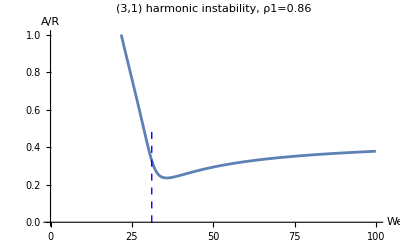

```mathematica
list1=Table[{we,epssol[rho1,rho2,3,we]},{we,0.01,100,0.1}];
minwe=First[First[MinimalBy[list1,#[[2]]&]]];
ListLinePlot[{list1},PlotRange->{{0,100},{0,1}},LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",20},Epilog->{{Blue,Dashed,Line[{{wem,0},{wem,0.5}}]}},PlotLabel->"(3,1) harmonic instability, ρ1="<>ToString[rho1],AxesLabel->{"We","A/R"}]
```

```mathematica
list04=list1;
```

```mathematica
rho1
```

0.4

```mathematica
rho2
```

0.6

```mathematica
1-rho1
```

0.14

```mathematica
list05=list1;
```

```mathematica
list02=list1;
```

```mathematica
list086=list1;
```

```mathematica
minwe
```

36.91

```mathematica
wem
```

31.0881

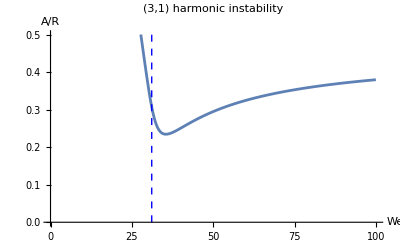

```mathematica
ListLinePlot[{list086,list04},PlotRange->{{0,100},{0,0.5}},LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",20},Epilog->{{Blue,Dashed,Line[{{weres,0},{weres,0.5}}]}},PlotLabel->"(3,1) harmonic instability",AxesLabel->{"We","A/R"}]
```

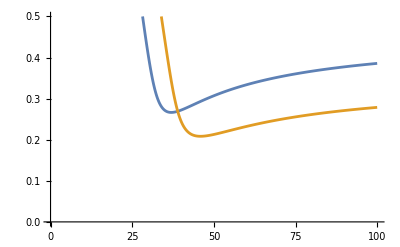

```mathematica
ListLinePlot[{list086,list02},PlotRange->{{0,100},{0,0.5}}]
```

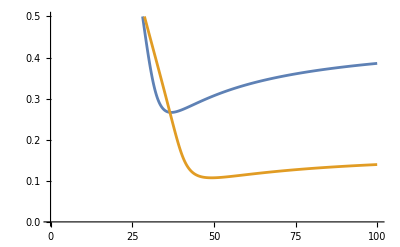

```mathematica
ListLinePlot[{list086,list0},PlotRange->{{0,100},{0,0.5}}]
```

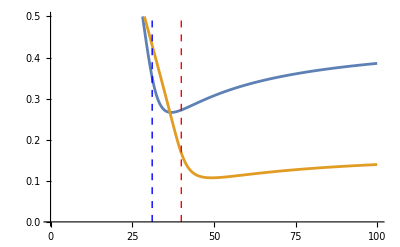

```mathematica
ListLinePlot[{list086,list0},PlotRange->{{0,100},{0,0.5}},Epilog->{{Blue,Dashed,Line[{{wem,0},{wem,0.5}}]},{Red,Dashed,Line[{{40,0},{40,0.5}}]}}]
```

```mathematica
Graphics[ListLinePlot[{list086,list0},PlotRange->{{0,100},{0,0.5}}],Line[{{wem,0},{wem,0.5}}]]
```

-Graphics-

```mathematica
dat
```

{0.00213357,1.59235,-34.2731,-0.159306,0.471291,0,0.0822192,40,77/256}

```mathematica
Solve[2/3*Pi*r^3==49.27,r]
```

{{r→-1.43267-2.48145 ⅈ},{r→-1.43267+2.48145 ⅈ},{r→2.86533}}

```mathematica
(4*9.8/(2*Pi*42)^2)/(2.87/1000)//N
```

0.196131

## For experiment

```mathematica
Solve[2/3*Pi*r^3==49.27,r]
```

{{r→-1.43267-2.48145 ⅈ},{r→-1.43267+2.48145 ⅈ},{r→2.86533}}

```mathematica
weber=(ρ1+ρ2)*(2*Pi*f)^2*rad^3/σ/.{ρ1->6440,ρ2->1040,rad->2.87/1000,σ->0.503,f->42}
```

24.4815

```mathematica
ρ1d=ρ1/(ρ1+ρ2)/.{ρ1->6440,ρ2->1040}//N
```

0.860963

```mathematica
ρ2d=ρ2/(ρ1+ρ2)/.{ρ1->6440,ρ2->1040}//N
```

0.139037

```mathematica
weres=(m(m+1)(m^2+m-2))/(ρ1d*(m+1)+ρ2d*m)/.{m->3}(*liquid metal*)
```

31.0803

```mathematica
weres=(m(m+1)(m^2+m-2))/(0*(m+1)+1*m)/.{m->3}(*bubble*)
```

40

```mathematica
ohn=(0.001+0.0024)/(√(1040+6440)*2.87*10^-3*0.403)
```

0.0339892

## Data save

```mathematica
list0={{0.01,50.11390475436088},{0.11,15.091024480099005},{0.21000000000000002,10.908395732423408},{0.31000000000000005,8.96693016572571},{0.41000000000000003,7.787273674819429},{0.51,6.973384824921271},{0.6100000000000001,6.368157159303731},{0.7100000000000001,5.895193905258583},{0.81,5.512288503100336},{0.91,5.193971087134874},{1.01,4.9238396273687925},{1.11,4.690790524477809},{1.2100000000000002,4.487002989435076},{1.31,4.3067878318313095},{1.4100000000000001,4.1458941358979535},{1.51,4.001073057179041},{1.61,3.869793144317821},{1.7100000000000002,3.750048663369997},{1.81,3.6402270235706444},{1.9100000000000001,3.5390149071496917},{2.01,3.4453304200977364},{2.11,3.358273146874692},{2.21,3.2770867802309143},{2.31,3.2011307474734787},{2.41,3.1298583804830193},{2.51,3.0627999173774954},{2.61,2.9995491206555527},{2.71,2.939752636196048},{2.81,2.8831014533597337},{2.91,2.8293239927896687},{3.01,2.7781804674730672},{3.11,2.72945824880634},{3.21,2.6829680325797747},{3.31,2.6385406466234014},{3.41,2.596024376920756},{3.51,2.555282715508918},{3.61,2.516192453708494},{3.71,2.478642059786921},{3.81,2.4425302922238727},{3.91,2.4077650091731355},{4.01,2.374262142130485},{4.11,2.3419448076893934},{4.21,2.3107425359460936},{4.31,2.2805905978669934},{4.41,2.2514294169558053},{4.51,2.223204053009022},{4.61,2.1958637477452543},{4.71,2.169361523728631},{4.8100000000000005,2.14365382935079},{4.91,2.1187002237464507},{5.01,2.0944630964387554},{5.11,2.070907417277745},{5.21,2.0480005128768544},{5.3100000000000005,2.0257118662906324},{5.41,2.004012937130271},{5.51,1.9828769996967015},{5.61,1.9622789970358412},{5.71,1.9421954090969016},{5.8100000000000005,1.9226041334103596},{5.91,1.9034843769038983},{6.01,1.884816557647657},{6.11,1.866582215469033},{6.21,1.848763930505694},{6.3100000000000005,1.8313452488765476},{6.41,1.8143106147466934},{6.51,1.797645308146066},{6.61,1.7813353879743514},{6.71,1.7653676396883853},{6.8100000000000005,1.749729527223878},{6.91,1.7344091487521127},{7.01,1.7193951959151013},{7.11,1.704676916220399},{7.21,1.6902440783100334},{7.3100000000000005,1.6760869398473772},{7.41,1.6621962177917884},{7.51,1.6485630608538933},{7.61,1.635179023944847},{7.71,1.622036044451107},{7.8100000000000005,1.609126420182481},{7.91,1.5964427888556674},{8.01,1.5839781089884446},{8.11,1.571725642091236},{8.21,1.5596789360531427},{8.31,1.5478318096288506},{8.41,1.5361783379411773},{8.51,1.5247128389215518},{8.61,1.5134298606175083},{8.71,1.502324169302382},{8.81,1.4913907383279388},{8.91,1.4806247376656507},{9.01,1.4700215240868741},{9.11,1.4595766319362748},{9.21,1.4492857644565793},{9.31,1.4391447856261068},{9.41,1.4291497124736214},{9.51,1.4192967078378342},{9.610000000000001,1.4095820735414504},{9.71,1.4000022439519781},{9.81,1.3905537799036425},{9.91,1.381233362956699},{10.01,1.3720377899722116},{10.110000000000001,1.3629639679819952},{10.21,1.3540089093349148},{10.31,1.3451697271021008},{10.41,1.3364436307248997},{10.51,1.3278279218905393},{10.610000000000001,1.3193199906215414},{10.71,1.3109173115659034},{10.81,1.3026174404759678},{10.91,1.294418010864728},{11.01,1.28631673082909},{11.110000000000001,1.2783113800303143},{11.21,1.2703998068225217},{11.31,1.262579925520745},{11.41,1.2548497138005743},{11.51,1.2472072102219605},{11.610000000000001,1.2396505118702241},{11.71,1.2321777721077574},{11.81,1.2247871984303258},{11.91,1.21747705042226},{12.01,1.2102456378051818},{12.110000000000001,1.2030913185752405},{12.21,1.1960124972241506},{12.31,1.1890076230396},{12.41,1.1820751884808722},{12.51,1.1752137276257735},{12.610000000000001,1.1684218146851864},{12.71,1.1616980625817939},{12.81,1.1550411215897125},{12.91,1.1484496780319706},{13.01,1.1419224530329393},{13.110000000000001,1.1354582013229917},{13.21,1.1290557100928174},{13.31,1.1227137978949715},{13.41,1.1164313135903623},{13.51,1.1102071353375198},{13.610000000000001,1.1040401696225985},{13.71,1.0979293503281835},{13.81,1.0918736378390723},{13.91,1.085872018183307},{14.01,1.0799235022068159},{14.110000000000001,1.07402712478012},{14.21,1.068181944035635},{14.31,1.0623870406341787},{14.41,1.0566415170593666},{14.51,1.0509444969386452},{14.610000000000001,1.0452951243897777},{14.71,1.0396925633916565},{14.81,1.0341359971783732},{14.91,1.0286246276555342},{15.01,1.023157674837855},{15.110000000000001,1.0177343763071192},{15.21,1.0123539866896285},{15.31,1.0070157771523205},{15.41,1.0017190349167588},{15.51,0.9964630627902527},{15.610000000000001,0.9912471787133875},{15.71,0.9860707153232882},{15.81,0.9809330195319661},{15.91,0.9758334521191357},{16.01,0.9707713873389077},{16.110000000000003,0.9657462125398011},{16.21,0.9607573277975395},{16.310000000000002,0.9558041455601174},{16.410000000000004,0.9508860903046531},{16.51,0.9460025982055613},{16.610000000000003,0.9411531168136014},{16.71,0.9363371047453763},{16.810000000000002,0.9315540313828796},{16.910000000000004,0.9268033765826984},{17.01,0.9220846303945059},{17.110000000000003,0.9173972927884881},{17.21,0.9127408733913638},{17.310000000000002,0.9081148912306772},{17.410000000000004,0.9035188744870497},{17.51,0.8989523602540953},{17.610000000000003,0.8944148943057154},{17.71,0.8899060308704994},{17.810000000000002,0.8854253324129703},{17.910000000000004,0.8809723694214273},{18.01,0.8765467202021415},{18.110000000000003,0.8721479706796788},{18.21,0.8677757142031264},{18.310000000000002,0.8634295513580144},{18.410000000000004,0.8591090897837262},{18.51,0.8548139439962062},{18.610000000000003,0.8505437352157745},{18.71,0.8462980911998719},{18.810000000000002,0.8420766460805614},{18.910000000000004,0.837879040206621},{19.01,0.833704919990067},{19.110000000000003,0.8295539377569581},{19.210000000000004,0.8254257516023293},{19.310000000000002,0.8213200252491178},{19.410000000000004,0.8172364279109415},{19.51,0.8131746341586027},{19.610000000000003,0.8091343237901876},{19.710000000000004,0.8051151817046432},{19.810000000000002,0.8011168977787138},{19.910000000000004,0.7971391667471237},{20.01,0.7931816880859012},{20.110000000000003,0.7892441658987345},{20.210000000000004,0.7853263088062654},{20.310000000000002,0.7814278298382181},{20.410000000000004,0.7775484463282741},{20.51,0.7736878798116009},{20.610000000000003,0.7698458559249487},{20.710000000000004,0.7660221043092312},{20.810000000000002,0.7622163585145103},{20.910000000000004,0.7584283559073057},{21.01,0.7546578375801559},{21.110000000000003,0.750904548263356},{21.210000000000004,0.747168236238804},{21.310000000000002,0.7434486532558875},{21.410000000000004,0.7397455544493445},{21.51,0.736058698259037},{21.610000000000003,0.7323878463515736},{21.710000000000004,0.7287327635437256},{21.810000000000002,0.7250932177275765},{21.910000000000004,0.721468979797352},{22.01,0.7178598235778754},{22.110000000000003,0.7142655257545983},{22.210000000000004,0.7106858658051559},{22.310000000000002,0.7071206259323988},{22.410000000000004,0.7035695909988547},{22.51,0.7000325484625749},{22.610000000000003,0.696509288314321},{22.710000000000004,0.6929996030160509},{22.810000000000002,0.6895032874406619},{22.910000000000004,0.6860201388129512},{23.01,0.6825499566517561},{23.110000000000003,0.6790925427132359},{23.210000000000004,0.6756477009352599},{23.310000000000002,0.6722152373828656},{23.410000000000004,0.6687949601947544},{23.51,0.6653866795307918},{23.610000000000003,0.661990207520479},{23.710000000000004,0.6586053582123665},{23.810000000000002,0.65523194752438},{23.910000000000004,0.6518697931950271},{24.01,0.648518714735462},{24.110000000000003,0.6451785333823743},{24.210000000000004,0.6418490720516822},{24.310000000000002,0.6385301552929997},{24.410000000000004,0.635221609244857},{24.51,0.6319232615906478},{24.610000000000003,0.6286349415152811},{24.710000000000004,0.625356479662517},{24.810000000000002,0.6220877080929629},{24.910000000000004,0.6188284602427115},{25.01,0.6155785708825984},{25.110000000000003,0.6123378760780632},{25.210000000000004,0.6091062131495935},{25.310000000000002,0.6058834206337352},{25.410000000000004,0.6026693382446524},{25.51,0.5994638068362206},{25.610000000000003,0.5962666683646379},{25.710000000000004,0.5930777658515407},{25.810000000000002,0.5898969433476084},{25.910000000000004,0.586724045896647},{26.01,0.5835589195001358},{26.110000000000003,0.5804014110822315},{26.210000000000004,0.5772513684552127},{26.310000000000002,0.5741086402853619},{26.410000000000004,0.5709730760592723},{26.51,0.5678445260505736},{26.610000000000003,0.564722841287071},{26.710000000000004,0.5616078735182903},{26.810000000000002,0.558499475183427},{26.910000000000004,0.5553974993796947},{27.01,0.5523017998310719},{27.110000000000003,0.5492122308574466},{27.210000000000004,0.5461286473441602},{27.310000000000002,0.5430509047119517},{27.410000000000004,0.5399788588873076},{27.51,0.536912366273223},{27.610000000000003,0.533851283720381},{27.710000000000004,0.5307954684987596},{27.810000000000002,0.5277447782696779},{27.910000000000004,0.5246990710582965},{28.01,0.5216582052265847},{28.110000000000003,0.5186220394467771},{28.210000000000004,0.5155904326753381},{28.310000000000002,0.5125632441274595},{28.410000000000004,0.5095403332521177},{28.51,0.5065215597077227},{28.610000000000003,0.5035067833383924},{28.710000000000004,0.5004958641508889},{28.810000000000002,0.49748866229226285},{28.910000000000004,0.4944850380282502},{29.01,0.4914848517224737},{29.110000000000003,0.4884879638165083},{29.210000000000004,0.4854942348108719},{29.310000000000002,0.48250352524701234},{29.410000000000004,0.4795156956903661},{29.51,0.476530606714573},{29.610000000000003,0.47354811888693843},{29.710000000000004,0.470568092755244},{29.810000000000002,0.4675903888360152},{29.910000000000004,0.4646148676043674},{30.01,0.4616413894855603},{30.110000000000003,0.4586698148484043},{30.210000000000004,0.45570000400067356},{30.310000000000002,0.45273181718669786},{30.410000000000004,0.449765114587316},{30.51,0.4467997563223946},{30.610000000000003,0.4438356024561313},{30.710000000000004,0.4408725130053814},{30.810000000000002,0.43791034795126943},{30.910000000000004,0.43494896725436916},{31.01,0.4319882308737598},{31.110000000000003,0.42902799879029585},{31.210000000000004,0.4260681310344545},{31.310000000000002,0.42310848771915954},{31.410000000000004,0.4201489290780129},{31.51,0.41718931550940436},{31.610000000000003,0.41422950762701133},{31.710000000000004,0.4112693663172433},{31.810000000000002,0.40830875280423606},{31.910000000000004,0.4053475287230523},{32.01,0.4023855562018016},{32.11,0.39942269795345675},{32.21,0.3964588173782073},{32.31,0.39349377867726704},{32.41,0.39052744697912833},{32.51,0.3875596884793432},{32.61,0.3845903705950016},{32.71,0.3816193621351793},{32.81,0.37864653348873206},{32.91,0.3756717568309337},{33.01,0.37269490635057506},{33.11,0.36971585849928185},{33.21,0.36673449226494914},{33.31,0.36375068947134975},{33.41,0.36076433510613704},{33.51,0.35777531767964416},{33.61,0.35478352961706894},{33.71,0.35178886768683704},{33.81,0.3487912334681492},{33.91,0.34579053386094566},{34.01,0.34278668164175574},{34.11,0.33977959606915153},{34.21,0.3367692035427808},{34.31,0.33375543832022},{34.41,0.3307382432961617},{34.51,0.32771757084872305},{34.61,0.3246933837579378},{34.71,0.3216656562017609},{34.81,0.31863437483517026},{34.91,0.3155995399581884},{35.01,0.3125611667788496},{35.11,0.3095192867773081},{35.21,0.30647394917739107},{35.31,0.30342522253193976},{35.41,0.30037319642823046},{35.51,0.29731798331959797},{35.61,0.2942597204890734},{35.71,0.2911985721503614},{35.81,0.2881347316907836},{35.91,0.28506842405986066},{36.01,0.28199990830595123},{36.11,0.2789294802617542},{36.21,0.2758574753774579},{36.31,0.27278427169782216},{36.41,0.2697102929764352},{36.51,0.2666360119167424},{36.61,0.2635619535251156},{36.71,0.260488698556168},{36.81,0.2574168870246673},{36.91,0.2543472217517089},{37.01,0.25128047190528263},{37.11,0.2482174764869982},{37.21,0.24515914770759453},{37.31,0.24210647418405284},{37.41,0.23906052388083965},{37.51,0.23602244670728026},{37.61,0.23299347667265827},{37.71,0.22997493349080073},{37.81,0.22696822351720575},{37.91,0.2239748398948695},{38.01,0.22099636178064339},{38.11,0.21803445252304934},{38.21,0.21509085666589678},{38.31,0.21216739566066445},{38.410000000000004,0.20926596218524546},{38.51,0.20638851298795466},{38.61,0.20353706020405815},{38.71,0.20071366112754357},{38.81,0.1979204064629853},{38.910000000000004,0.19515940713022764},{39.01,0.1924327797466762},{39.11,0.1897426309661524},{39.21,0.18709104090690631},{39.31,0.18448004595148565},{39.410000000000004,0.18191162124452354},{39.51,0.1793876632479792},{39.61,0.1769099727341291},{39.71,0.17448023860246883},{39.81,0.17210002289632867},{39.910000000000004,0.16977074736817416},{40.01,0.16749368190015676},{40.11,0.16526993503051715},{40.21,0.16310044676993463},{40.31,0.16098598381857646},{40.410000000000004,0.1589271372185901},{40.51,0.15692432240225127},{40.61,0.15497778152683211},{40.71,0.15308758792674654},{40.81,0.15125365246412412},{40.910000000000004,0.14947573152217464},{41.01,0.14775343636209354},{41.11,0.14608624355350758},{41.21,0.14447350618950822},{41.31,0.14291446560856555},{41.410000000000004,0.141408263365096},{41.51,0.1399539532160702},{41.61,0.13855051292070483},{41.71,0.13719685568205045},{41.81,0.1358918410914891},{41.910000000000004,0.1346342854684098},{42.01,0.13342297151658408},{42.11,0.13225665724528193},{42.21,0.1311340841264935},{42.31,0.13005398447954808},{42.410000000000004,0.12901508809094056},{42.51,0.12801612809042154},{42.61,0.12705584611462983},{42.71,0.12613299679705586},{42.81,0.12524635162826558},{42.910000000000004,0.12439470223344494},{43.01,0.12357686311578919},{43.11,0.12279167391438095},{43.21,0.1220380012242704},{43.31,0.12131474002474532},{43.410000000000004,0.12062081475948001},{43.51,0.11995518010956513},{43.61,0.11931682149749774},{43.71,0.11870475535717416},{43.81,0.11811802920187378},{43.910000000000004,0.11755572151922208},{44.01,0.11701694151922928},{44.11,0.1165008287587555},{44.21,0.11600655266317828},{44.31,0.11553331196364754},{44.410000000000004,0.11508033406611443},{44.51,0.11464687436631249},{44.61,0.11423221552304909},{44.71,0.1138356667005237},{44.81,0.1134565627889186},{44.910000000000004,0.1130942636111943},{45.01,0.11274815312285638},{45.11,0.11241763861042899},{45.21,0.11210214989346186},{45.31,0.11180113853410009},{45.410000000000004,0.11151407705754895},{45.51,0.11124045818615796},{45.61,0.11097979408932156},{45.71,0.11073161565093662},{45.81,0.11049547175576459},{45.910000000000004,0.11027092859570765},{46.01,0.1100575689967201},{46.11,0.10985499176683043},{46.21,0.10966281106554167},{46.31,0.1094806557947021},{46.410000000000004,0.10930816901079247},{46.51,0.10914500735845369},{46.61,0.10899084052497893},{46.71,0.10884535071541293},{46.81,0.10870823214783495},{46.910000000000004,0.10857919056835082},{47.01,0.10845794278527889},{47.11,0.1083442162219853},{47.21,0.10823774848780204},{47.31,0.10813828696644742},{47.410000000000004,0.10804558842136029},{47.51,0.10795941861735675},{47.61,0.10787955195801885},{47.71,0.10780577113822998},{47.81,0.10773786681127927},{47.910000000000004,0.10767563726996743},{48.01,0.10761888814115808},{48.11,0.10756743209323259},{48.21,0.10752108855592035},{48.31,0.1074796834519924},{48.410000000000004,0.10744304894032168},{48.51,0.10741102316983028},{48.61,0.1073834500438599},{48.71,0.107360178994519},{48.81,0.10734106476657641},{48.910000000000004,0.10732596721048768},{49.01,0.10731475108415679},{49.11,0.10730728586305174},{49.21,0.10730344555830791},{49.31,0.10730310854246866},{49.410000000000004,0.10730615738252713},{49.51,0.1073124786799476},{49.61,0.10732196291735864},{49.71,0.10733450431162377},{49.81,0.10735000067300804},{49.910000000000004,0.1073683532701717},{50.01,0.1073894667007338},{50.11,0.10741324876716007},{50.21,0.10743961035774106},{50.31,0.10746846533243591},{50.410000000000004,0.1074997304133685},{50.51,0.10753332507977169},{50.61,0.10756917146718481},{50.71,0.10760719427071855},{50.81,0.10764732065220972},{50.910000000000004,0.1076894801510966},{51.01,0.10773360459885327},{51.11,0.10777962803682858},{51.21,0.10782748663734286},{51.31,0.10787711862790153},{51.410000000000004,0.107928464218392},{51.51,0.10798146553113558},{51.61,0.10803606653367259},{51.71,0.10809221297416398},{51.81,0.10814985231929831},{51.910000000000004,0.1082089336945979},{52.01,0.10826940782702275},{52.11,0.10833122698977557},{52.21,0.10839434494921542},{52.31,0.10845871691379166},{52.410000000000004,0.10852429948491425},{52.51,0.10859105060967944},{52.61,0.10865892953537443},{52.71,0.10872789676568725},{52.81,0.10879791401855184},{52.910000000000004,0.10886894418556117},{53.01,0.10894095129288445},{53.11,0.10901390046362694},{53.21,0.1090877578815742},{53.31,0.10916249075626433},{53.410000000000004,0.10923806728933509},{53.51,0.10931445664209438},{53.61,0.10939162890426543},{53.71,0.1094695550638596},{53.81,0.10954820697813215},{53.910000000000004,0.10962755734557814},{54.01,0.1097075796789272},{54.11,0.10978824827909825},{54.21,0.10986953821007625},{54.31,0.1099514252746753},{54.410000000000004,0.11003388599115341},{54.51,0.11011689757064598},{54.61,0.11020043789538661},{54.71,0.11028448549768456},{54.81,0.11036901953963026},{54.910000000000004,0.11045401979350086},{55.01,0.11053946662283927},{55.11,0.11062534096418096},{55.21,0.1107116243094045},{55.31,0.11079829868868184},{55.410000000000004,0.1108853466540062},{55.51,0.11097275126327595},{55.61,0.11106049606491349},{55.71,0.11114856508299971},{55.81,0.11123694280290475},{55.910000000000004,0.11132561415739665},{56.01,0.11141456451321066},{56.11,0.11150377965806214},{56.21,0.11159324578808696},{56.31,0.11168294949569386},{56.410000000000004,0.11177287775781389},{56.51,0.11186301792453263},{56.61,0.11195335770809131},{56.71,0.11204388517224394},{56.81,0.11213458872195722},{56.910000000000004,0.11222545709344166},{57.01,0.1123164793445017},{57.11,0.1124076448451938},{57.21,0.11249894326878165},{57.31,0.11259036458297794},{57.410000000000004,0.11268189904146293},{57.51,0.11277353717566992},{57.61,0.11286526978682858},{57.71,0.11295708793825704},{57.81,0.11304898294789427},{57.910000000000004,0.1131409463810646},{58.01,0.11323297004346611},{58.11,0.11332504597437563},{58.21,0.1134171664400628},{58.31,0.11350932392740605},{58.410000000000004,0.11360151113770377},{58.51,0.11369372098067423},{58.61,0.11378594656863761},{58.71,0.11387818121087429},{58.81,0.11397041840815347},{58.910000000000004,0.11406265184742653},{59.01,0.11415487539667939},{59.11,0.11424708309993908},{59.21,0.11433926917242908},{59.31,0.11443142799586864},{59.410000000000004,0.1145235541139116},{59.51,0.11461564222771978},{59.61,0.1147076871916669},{59.71,0.11479968400916864},{59.81,0.11489162782863487},{59.910000000000004,0.11498351393953998},{60.01,0.11507533776860777},{60.11,0.11516709487610684},{60.21,0.11525878095225349},{60.31,0.11535039181371823},{60.410000000000004,0.11544192340023295},{60.51,0.11553337177129533},{60.61,0.11562473310296772},{60.71,0.11571600368476721},{60.81,0.11580717991664428},{60.910000000000004,0.11589825830604714},{61.01,0.11598923546506915},{61.11,0.11608010810767681},{61.21,0.11617087304701565},{61.31,0.11626152719279179},{61.410000000000004,0.1163520675487268},{61.51,0.11644249121008363},{61.61,0.1165327953612613},{61.71,0.11662297727345658},{61.81,0.11671303430239025},{61.910000000000004,0.11680296388609626},{62.01,0.1168927635427718},{62.11,0.1169824308686864},{62.21,0.1170719635361484},{62.31,0.11716135929152698},{62.410000000000004,0.11725061595332811},{62.51,0.11733973141032296},{62.61,0.11742870361972689},{62.71,0.11751753060542798},{62.81,0.11760621045626318},{62.910000000000004,0.11769474132434098},{63.01,0.1177831214234092},{63.11,0.11787134902726647},{63.21,0.11795942246821615},{63.31,0.11804734013556169},{63.410000000000004,0.11813510047414172},{63.51,0.11822270198290441},{63.61,0.1183101432135193},{63.71,0.118397422769026},{63.81,0.11848453930251841},{63.910000000000004,0.1185714915158637},{64.01,0.11865827815845478},{64.11000000000001,0.11874489802599557},{64.21000000000001,0.11883134995931789},{64.31,0.11891763284322938},{64.41000000000001,0.11900374560539125},{64.51,0.11908968721522523},{64.61000000000001,0.11917545668284887},{64.71000000000001,0.11926105305803836},{64.81,0.11934647542921806},{64.91000000000001,0.11943172292247614},{65.01,0.11951679470060546},{65.11000000000001,0.11960168996216904},{65.21000000000001,0.11968640794058953},{65.31,0.11977094790326182},{65.41000000000001,0.11985530915068834},{65.51,0.11993949101563643},{65.61000000000001,0.12002349286231692},{65.71000000000001,0.12010731408558371},{65.81,0.12019095411015354},{65.91000000000001,0.12027441238984542},{66.01,0.12035768840683926},{66.11000000000001,0.12044078167095315},{66.21000000000001,0.12052369171893884},{66.31,0.12060641811379474},{66.41000000000001,0.12068896044409629},{66.51,0.12077131832334287},{66.61000000000001,0.12085349138932117},{66.71000000000001,0.12093547930348425},{66.81,0.12101728175034618},{66.91000000000001,0.1210988984368915},{67.01,0.12118032909199956},{67.11000000000001,0.12126157346588287},{67.21000000000001,0.1213426313295394},{67.31,0.1214235024742184},{67.41000000000001,0.12150418671089935},{67.51,0.12158468386978369},{67.61000000000001,0.12166499379979899},{67.71000000000001,0.12174511636811537},{67.81,0.12182505145967366},{67.91000000000001,0.12190479897672508},{68.01,0.12198435883838218},{68.11000000000001,0.12206373098018071},{68.21000000000001,0.12214291535365213},{68.31,0.1222219119259065},{68.41000000000001,0.12230072067922554},{68.51,0.1223793416106654},{68.61000000000001,0.12245777473166922},{68.71000000000001,0.12253602006768892},{68.81,0.12261407765781616},{68.91000000000001,0.1226919475544222},{69.01,0.1227696298228064},{69.11000000000001,0.12284712454085316},{69.21000000000001,0.12292443179869715},{69.31,0.12300155169839652},{69.41000000000001,0.12307848435361395},{69.51,0.1231552298893053},{69.61000000000001,0.1232317884414158},{69.71000000000001,0.12330816015658334},{69.81,0.123384345191849},{69.91000000000001,0.12346034371437432},{70.01,0.12353615590116544},{70.11000000000001,0.12361178193880372},{70.21000000000001,0.12368722202318272},{70.31,0.12376247635925157},{70.41000000000001,0.12383754516076426},{70.51,0.12391242865003498},{70.61000000000001,0.12398712705769917},{70.71000000000001,0.12406164062248037},{70.81,0.12413596959096235},{70.91000000000001,0.12421011421736682},{71.01,0.12428407476333635},{71.11000000000001,0.12435785149772227},{71.21000000000001,0.12443144469637779},{71.31,0.12450485464195582},{71.41000000000001,0.1245780816237116},{71.51,0.12465112593731002},{71.61000000000001,0.12472398788463739},{71.71000000000001,0.12479666777361771},{71.81,0.12486916591803321},{71.91000000000001,0.1249414826373491},{72.01,0.12501361825654247},{72.11000000000001,0.12508557310593518},{72.21000000000001,0.12515734752103064},{72.31,0.12522894184235447},{72.41000000000001,0.1253003564152989},{72.51,0.12537159158997072},{72.61000000000001,0.1254426477210429},{72.71000000000001,0.1255135251676097},{72.81,0.1255842242930449},{72.91000000000001,0.12565474546486383},{73.01,0.1257250890545882},{73.11000000000001,0.12579525543761436},{73.21000000000001,0.12586524499308438},{73.31,0.12593505810376046},{73.41000000000001,0.1260046951559021},{73.51,0.12607415653914608},{73.61000000000001,0.12614344264638946},{73.71000000000001,0.1262125538736751},{73.81,0.12628149062008},{73.91000000000001,0.1263502532876063},{74.01,0.12641884228107453},{74.11000000000001,0.12648725800801985},{74.21000000000001,0.12655550087859022},{74.31,0.12662357130544732},{74.41000000000001,0.1266914697036697},{74.51,0.12675919649065798},{74.61000000000001,0.12682675208604266},{74.71000000000001,0.12689413691159385},{74.81,0.12696135139113304},{74.91000000000001,0.12702839595044726},{75.01,0.127095271017205},{75.11000000000001,0.12716197702087412},{75.21000000000001,0.12722851439264185},{75.31,0.12729488356533664},{75.41000000000001,0.1273610849733516},{75.51,0.12742711905257018},{75.61000000000001,0.1274929862402932},{75.71000000000001,0.12755868697516795},{75.81,0.12762422169711865},{75.91000000000001,0.12768959084727888},{76.01,0.1277547948679253},{76.11000000000001,0.1278198342024132},{76.21000000000001,0.12788470929511342},{76.31,0.12794942059135098},{76.41000000000001,0.12801396853734479},{76.51,0.12807835358014927},{76.61000000000001,0.12814257616759706},{76.71000000000001,0.12820663674824315},{76.81000000000002,0.12827053577131045},{76.91000000000001,0.12833427368663655},{77.01,0.1283978509446219},{77.11000000000001,0.12846126799617907},{77.21000000000001,0.12852452529268343},{77.31000000000002,0.12858762328592482},{77.41000000000001,0.1286505624280606},{77.51,0.1287133431715697},{77.61000000000001,0.12877596596920773},{77.71000000000001,0.12883843127396352},{77.81000000000002,0.12890073953901626},{77.91000000000001,0.12896289121769405},{78.01,0.12902488676343335},{78.11000000000001,0.1290867266297393},{78.21000000000001,0.12914841127014737},{78.31000000000002,0.12920994113818549},{78.41000000000001,0.12927131668733757},{78.51,0.12933253837100758},{78.61000000000001,0.12939360664248475},{78.71000000000001,0.12945452195490964},{78.81000000000002,0.12951528476124077},{78.91000000000001,0.1295758955142226},{79.01,0.12963635466635381},{79.11000000000001,0.12969666266985672},{79.21000000000001,0.12975681997664737},{79.31000000000002,0.12981682703830633},{79.41000000000001,0.12987668430605037},{79.51,0.12993639223070474},{79.61000000000001,0.1299959512626763},{79.71000000000001,0.13005536185192718},{79.81000000000002,0.13011462444794925},{79.91000000000001,0.13017373949973926},{80.01,0.13023270745577456},{80.11000000000001,0.13029152876398956},{80.21000000000001,0.13035020387175267},{80.31000000000002,0.13040873322584398},{80.41000000000001,0.13046711727243357},{80.51,0.1305253564570602},{80.61000000000001,0.13058345122461085},{80.71000000000001,0.13064140201930052},{80.81000000000002,0.13069920928465295},{80.91000000000001,0.13075687346348147},{81.01,0.13081439499787062},{81.11000000000001,0.13087177432915834},{81.21000000000001,0.1309290118979184},{81.31000000000002,0.1309861081439435},{81.41000000000001,0.13104306350622905},{81.51,0.13109987842295676},{81.61000000000001,0.13115655333147958},{81.71000000000001,0.13121308866830628},{81.81000000000002,0.1312694848690871},{81.91000000000001,0.13132574236859929},{82.01,0.1313818616007335},{82.11000000000001,0.13143784299848044},{82.21000000000001,0.13149368699391772},{82.31000000000002,0.13154939401819749},{82.41000000000001,0.1316049645015341},{82.51,0.13166039887319245},{82.61000000000001,0.13171569756147633},{82.71000000000001,0.13177086099371746},{82.81000000000002,0.13182588959626482},{82.91000000000001,0.13188078379447413},{83.01,0.13193554401269786},{83.11000000000001,0.13199017067427551},{83.21000000000001,0.1320446642015242},{83.31000000000002,0.1320990250157295},{83.41000000000001,0.1321532535371369},{83.51,0.13220735018494298},{83.61000000000001,0.13226131537728752},{83.71000000000001,0.13231514953124546},{83.81000000000002,0.1323688530628193},{83.91000000000001,0.13242242638693177},{84.01,0.1324758699174188},{84.11000000000001,0.13252918406702266},{84.21000000000001,0.1325823692473854},{84.31000000000002,0.1326354258690426},{84.41000000000001,0.13268835434141726},{84.51,0.13274115507281412},{84.61000000000001,0.13279382847041388},{84.71000000000001,0.13284637494026796},{84.81000000000002,0.13289879488729348},{84.91000000000001,0.1329510887152681},{85.01,0.1330032568268256},{85.11000000000001,0.13305529962345122},{85.21000000000001,0.13310721750547747},{85.31000000000002,0.13315901087208007},{85.41000000000001,0.133210680121274},{85.51,0.13326222564990983},{85.61000000000001,0.13331364785367036},{85.71000000000001,0.1333649471270671},{85.81000000000002,0.1334161238634372},{85.91000000000001,0.13346717845494066},{86.01,0.13351811129255728},{86.11000000000001,0.1335689227660842},{86.21000000000001,0.13361961326413344},{86.31000000000002,0.13367018317412943},{86.41000000000001,0.13372063288230718},{86.51,0.13377096277370998},{86.61000000000001,0.1338211732321877},{86.71000000000001,0.13387126464039512},{86.81000000000002,0.13392123737979028},{86.91000000000001,0.13397109183063316},{87.01,0.1340208283719843},{87.11000000000001,0.1340704473817038},{87.21000000000001,0.13411994923645007},{87.31000000000002,0.13416933431167916},{87.41000000000001,0.1342186029816439},{87.51,0.13426775561939322},{87.61000000000001,0.13431679259677168},{87.71000000000001,0.13436571428441899},{87.81000000000002,0.13441452105176974},{87.91000000000001,0.13446321326705324},{88.01,0.13451179129729335},{88.11000000000001,0.13456025550830858},{88.21000000000001,0.1346086062647121},{88.31000000000002,0.1346568439299121},{88.41000000000001,0.1347049688661119},{88.51,0.13475298143431066},{88.61000000000001,0.13480088199430354},{88.71000000000001,0.1348486709046825},{88.81000000000002,0.134896348522837},{88.91000000000001,0.13494391520495455},{89.01,0.13499137130602182},{89.11000000000001,0.13503871717982538},{89.21000000000001,0.1350859531789528},{89.31000000000002,0.1351330796547937},{89.41000000000001,0.13518009695754096},{89.51,0.13522700543619182},{89.61000000000001,0.13527380543854933},{89.71000000000001,0.1353204973112237},{89.81000000000002,0.13536708139963366},{89.91000000000001,0.13541355804800811},{90.01,0.13545992759938755},{90.11000000000001,0.1355061903956258},{90.21000000000001,0.13555234677739167},{90.31000000000002,0.13559839708417076},{90.41000000000001,0.1356443416542672},{90.51,0.13569018082480566},{90.61000000000001,0.13573591493173306},{90.71000000000001,0.13578154430982084},{90.81000000000002,0.1358270692926667},{90.91000000000001,0.1358724902126969},{91.01,0.13591780740116832},{91.11000000000001,0.1359630211881706},{91.21000000000001,0.1360081319026285},{91.31000000000002,0.136053139872304},{91.41000000000001,0.13609804542379875},{91.51,0.13614284888255637},{91.61000000000001,0.13618755057286494},{91.71000000000001,0.1362321508178593},{91.81000000000002,0.13627664993952365},{91.91000000000001,0.1363210482586941},{92.01,0.136365346095061},{92.11000000000001,0.13640954376717193},{92.21000000000001,0.13645364159243392},{92.31000000000002,0.13649763988711638},{92.41000000000001,0.13654153896635368},{92.51,0.13658533914414797},{92.61000000000001,0.13662904073337181},{92.71000000000001,0.1366726440457711},{92.81000000000002,0.13671614939196775},{92.91000000000001,0.13675955708146267},{93.01,0.13680286742263859},{93.11000000000001,0.1368460807227629},{93.21000000000001,0.13688919728799062},{93.31000000000002,0.13693221742336742},{93.41000000000001,0.1369751414328325},{93.51,0.13701796961922152},{93.61000000000001,0.13706070228426984},{93.71000000000001,0.13710333972861535},{93.81000000000002,0.13714588225180166},{93.91000000000001,0.13718833015228107},{94.01,0.13723068372741778},{94.11000000000001,0.13727294327349088},{94.21000000000001,0.13731510908569763},{94.31000000000002,0.13735718145815648},{94.41000000000001,0.1373991606839103},{94.51,0.1374410470549296},{94.61000000000001,0.13748284086211562},{94.71000000000001,0.13752454239530368},{94.81000000000002,0.1375661519432662},{94.91000000000001,0.13760766979371625},{95.01,0.13764909623331043},{95.11000000000001,0.13769043154765245},{95.21000000000001,0.13773167602129624},{95.31000000000002,0.13777282993774922},{95.41000000000001,0.13781389357947574},{95.51,0.13785486722790022},{95.61000000000001,0.13789575116341055},{95.71000000000001,0.13793654566536137},{95.81000000000002,0.13797725101207753},{95.91000000000001,0.1380178674808572},{96.01,0.1380583953479754},{96.11000000000001,0.13809883488868732},{96.21000000000001,0.13813918637723163},{96.31000000000002,0.13817945008683383},{96.41000000000001,0.13821962628970974},{96.51,0.13825971525706873},{96.61000000000001,0.13829971725911722},{96.71000000000001,0.13833963256506193},{96.81000000000002,0.13837946144311344},{96.91000000000001,0.13841920416048945},{97.01,0.1384588609834182},{97.11000000000001,0.1384984321771419},{97.21000000000001,0.1385379180059201},{97.31000000000002,0.13857731873303317},{97.41000000000001,0.13861663462078552},{97.51,0.1386558659305092},{97.61000000000001,0.13869501292256722},{97.71000000000001,0.13873407585635697},{97.81000000000002,0.13877305499031362},{97.91000000000001,0.13881195058191348},{98.01,0.13885076288767753},{98.11000000000001,0.1388894921631747},{98.21000000000001,0.13892813866302536},{98.31000000000002,0.13896670264090466},{98.41000000000001,0.13900518434954598},{98.51,0.13904358404074432},{98.61000000000001,0.1390819019653597},{98.71000000000001,0.13912013837332052},{98.81000000000002,0.13915829351362702},{98.91000000000001,0.1391963676343546},{99.01,0.13923436098265735},{99.11000000000001,0.1392722738047712},{99.21000000000001,0.13931010634601748},{99.31000000000002,0.1393478588508063},{99.41000000000001,0.13938553156263989},{99.51,0.1394231247241159},{99.61000000000001,0.1394606385769308},{99.71000000000001,0.13949807336188344},{99.81000000000002,0.13953542931887808},{99.91000000000001,0.13957270668692798}};
```

```mathematica
list02={{0.01,83.03403369924072},{0.11,25.002743093398422},{0.21000000000000002,18.071770970047723},{0.31000000000000005,14.854374265314386},{0.41000000000000003,12.899313789578416},{0.51,11.55035270460691},{0.6100000000000001,10.547163495711052},{0.7100000000000001,9.76315396042704},{0.81,9.128385372595117},{0.91,8.60065212175305},{1.01,8.15277437005431},{1.11,7.7663520786572295},{1.2100000000000002,7.428425062513857},{1.31,7.12956538282295},{1.4100000000000001,6.862728470685342},{1.51,6.622530308617176},{1.61,6.404775695978569},{1.7100000000000002,6.206140624697974},{1.81,6.023952589944162},{1.9100000000000001,5.856035036307357},{2.01,5.70059492290441},{2.11,5.556139957015379},{2.21,5.421416665998882},{2.31,5.295363377348609},{2.41,5.177074042559478},{2.51,5.065770067682115},{2.61,4.96077813690571},{2.71,4.861512578161827},{2.81,4.767461210598861},{2.91,4.678173889435993},{3.01,4.593253160844997},{3.11,4.5123465823165265},{3.21,4.435140368655677},{3.31,4.361354101346639},{3.41,4.29073629713402},{3.51,4.223060675601994},{3.61,4.158122999048697},{3.71,4.0957383837382295},{3.81,4.0357390016069115},{3.91,3.9779721071202525},{4.01,3.9222983362653654},{4.11,3.8685902343950027},{4.21,3.81673097739457},{4.31,3.766613256860398},{4.41,3.7181383049895538},{4.51,3.6712150389437426},{4.61,3.625759307759153},{4.71,3.5816932275831013},{4.8100000000000005,3.538944593246233},{4.91,3.497446356019346},{5.01,3.4571361589305023},{5.11,3.417955922289587},{5.21,3.3798514731305658},{5.3100000000000005,3.342772213173865},{5.41,3.306670820662695},{5.51,3.2715029820621164},{5.61,3.237227150148024},{5.71,3.203804325471151},{5.8100000000000005,3.171197858571825},{5.91,3.1393732706554904},{6.01,3.1082980907257762},{6.11,3.0779417074186766},{6.21,3.0482752339942447},{6.3100000000000005,3.019271385126295},{6.41,2.9909043642901927},{6.51,2.9631497606874913},{6.61,2.935984454766967},{6.71,2.9093865315070335},{6.8100000000000005,2.883335200716758},{6.91,2.857810723693556},{7.01,2.832794345646655},{7.11,2.8082682333579303},{7.21,2.7842154176068226},{7.3100000000000005,2.7606197399347394},{7.41,2.7374658033674306},{7.51,2.714738926752012},{7.61,2.692425102399254},{7.71,2.6705109567518894},{7.8100000000000005,2.6489837138266066},{7.91,2.6278311612013465},{8.01,2.6070416183409737},{8.11,2.5866039070735547},{8.21,2.5665073240466842},{8.31,2.546741615008703},{8.41,2.5272969507735383},{8.51,2.5081639047403548},{8.61,2.4893334318504623},{8.71,2.4707968488740493},{8.81,2.452545815928492},{8.91,2.4345723191382667},{9.01,2.416868654353985},{9.11,2.399427411854895},{9.21,2.3822414619653465},{9.31,2.3653039415213253},{9.41,2.348608241128278},{9.51,2.332147993156073},{9.610000000000001,2.3159170604211896},{9.71,2.299909525510077},{9.81,2.2841196807011643},{9.91,2.268542018446205},{10.01,2.253171222374616},{10.110000000000001,2.2380021587871446},{10.21,2.2230298686076884},{10.31,2.208249559764358},{10.41,2.193656599972963},{10.51,2.1792465098980105},{10.610000000000001,2.165014956668068},{10.71,2.1509577477239796},{10.81,2.1370708249798978},{10.91,2.123350259278487},{11.01,2.109792245122917},{11.110000000000001,2.096393095669451},{11.21,2.0831492379654986},{11.31,2.070057208419028},{11.41,2.0571136484861494},{11.51,2.044315300564535},{11.610000000000001,2.03165900408116},{11.71,2.0191416917635605},{11.81,2.00676038608451},{11.91,1.9945121958706498},{12.01,1.9823943130661845},{12.110000000000001,1.9704040096433306},{12.21,1.9585386346516922},{12.31,1.9467956113992313},{12.41,1.935172434757936},{12.51,1.923666668587705},{12.610000000000001,1.912275943272354},{12.71,1.900997953362006},{12.81,1.8898304553164695},{12.91,1.8787712653445137},{13.01,1.8678182573342508},{13.110000000000001,1.8569693608701066},{13.21,1.8462225593321167},{13.31,1.8355758880735258},{13.41,1.8250274326728952},{13.51,1.8145753272571306},{13.610000000000001,1.804217752892041},{13.71,1.7939529360372286},{13.81,1.7837791470622777},{13.91,1.7736946988213773},{14.01,1.7636979452836645},{14.110000000000001,1.7537872802167218},{14.21,1.7439611359207943},{14.31,1.7342179820114199},{14.41,1.7245563242482898},{14.51,1.7149747034082652},{14.610000000000001,1.705471694200583},{14.71,1.6960459042223857},{14.81,1.6866959729528042},{14.91,1.6774205707839092},{15.01,1.6682183980869334},{15.110000000000001,1.659088184312246},{15.21,1.650028687121633},{15.31,1.6410386915515112},{15.41,1.6321170092057675},{15.51,1.6232624774769817},{15.610000000000001,1.6144739587948453},{15.71,1.6057503399006503},{15.81,1.5970905311467747},{15.91,1.5884934658201384},{16.01,1.5799580994886544},{16.110000000000003,1.5714834093697465},{16.21,1.5630683937200418},{16.310000000000002,1.5547120712453957},{16.410000000000004,1.5464134805304368},{16.51,1.5381716794868632},{16.610000000000003,1.5299857448197514},{16.71,1.5218547715111732},{16.810000000000002,1.513777872320452},{16.910000000000004,1.5057541773004086},{17.01,1.497782833328988},{17.110000000000003,1.4898630036556766},{17.21,1.4819938674621473},{17.310000000000002,1.4741746194365952},{17.410000000000004,1.4664044693612484},{17.51,1.4586826417125605},{17.610000000000003,1.4510083752736143},{17.71,1.4433809227582814},{17.810000000000002,1.4357995504467076},{17.910000000000004,1.4282635378317063},{18.01,1.4207721772756627},{18.110000000000003,1.4133247736775683},{18.21,1.4059206441498162},{18.310000000000002,1.3985591177044097},{18.410000000000004,1.3912395349482458},{18.51,1.383961247787148},{18.610000000000003,1.3767236191383407},{18.71,1.369526022651067},{18.810000000000002,1.3623678424350598},{18.910000000000004,1.3552484727965963},{19.01,1.3481673179818665},{19.110000000000003,1.341123791927405},{19.210000000000004,1.334117318017341},{19.310000000000002,1.3271473288472282},{19.410000000000004,1.3202132659942358},{19.51,1.3133145797934755},{19.610000000000003,1.3064507291202598},{19.710000000000004,1.2996211811780893},{19.810000000000002,1.2928254112921749},{19.910000000000004,1.2860629027083093},{20.01,1.279333146396905},{20.110000000000003,1.2726356408620323},{20.210000000000004,1.2659698919552818},{20.310000000000002,1.2593354126942982},{20.410000000000004,1.252731723085828},{20.51,1.2461583499531292},{20.610000000000003,1.2396148267676053},{20.710000000000004,1.2331006934845175},{20.810000000000002,1.2266154963826488},{20.910000000000004,1.220158787907784},{21.01,1.2137301265198883},{21.110000000000003,1.2073290765438576},{21.210000000000004,1.20095520802373},{21.310000000000002,1.1946080965802446},{21.410000000000004,1.18828732327164},{21.51,1.1819924744575876},{21.610000000000003,1.1757231416661627},{21.710000000000004,1.1694789214637527},{21.810000000000002,1.1632594153278106},{21.910000000000004,1.1570642295223654},{22.01,1.1508929749761987},{22.110000000000003,1.1447452671636074},{22.210000000000004,1.1386207259876697},{22.310000000000002,1.1325189756659366},{22.410000000000004,1.1264396446184741},{22.51,1.1203823653581835},{22.610000000000003,1.1143467743833306},{22.710000000000004,1.1083325120722156},{22.810000000000002,1.1023392225799205},{22.910000000000004,1.0963665537370706},{23.01,1.0904141569505517},{23.110000000000003,1.084481687106125},{23.210000000000004,1.078568802472884},{23.310000000000002,1.072675164609504},{23.410000000000004,1.0668004382722314},{23.51,1.0609442913245628},{23.610000000000003,1.055106394648576},{23.710000000000004,1.0492864220578597},{23.810000000000002,1.0434840502120095},{23.910000000000004,1.0376989585326466},{24.01,1.0319308291209226},{24.110000000000003,1.0261793466764808},{24.210000000000004,1.0204441984178374},{24.310000000000002,1.0147250740041556},{24.410000000000004,1.009021665458387},{24.51,1.003333667091753},{24.610000000000003,0.9976607754295471},{24.710000000000004,0.9920026891382391},{24.810000000000002,0.9863591089538631},{24.910000000000004,0.9807297376116783},{25.01,0.9751142797770899},{25.110000000000003,0.9695124419778262},{25.210000000000004,0.9639239325373639},{25.310000000000002,0.9583484615096052},{25.410000000000004,0.9527857406148065},{25.51,0.9472354831767678},{25.610000000000003,0.9416974040612923},{25.710000000000004,0.9361712196159334},{25.810000000000002,0.9306566476110456},{25.910000000000004,0.9251534071821671},{26.01,0.9196612187737616},{26.110000000000003,0.9141798040843552},{26.210000000000004,0.9087088860131086},{26.310000000000002,0.9032481886078735},{26.410000000000004,0.8977974370147827},{26.51,0.8923563574294407},{26.610000000000003,0.8869246770497781},{26.710000000000004,0.8815021240306482},{26.810000000000002,0.8760884274402534},{26.910000000000004,0.8706833172184925},{27.01,0.8652865241373372},{27.110000000000003,0.8598977797633529},{27.210000000000004,0.8545168164224916},{27.310000000000002,0.849143367167298},{27.410000000000004,0.8437771657466844},{27.51,0.838417946578442},{27.610000000000003,0.8330654447246767},{27.710000000000004,0.8277193958703705},{27.810000000000002,0.8223795363052915},{27.910000000000004,0.8170456029094949},{28.01,0.8117173331426792},{28.110000000000003,0.8063944650376847},{28.210000000000004,0.8010767371984506},{28.310000000000002,0.7957638888027698},{28.410000000000004,0.7904556596102164},{28.51,0.7851517899756482},{28.610000000000003,0.7798520208687272},{28.710000000000004,0.7745560938999342},{28.810000000000002,0.7692637513536011},{28.910000000000004,0.7639747362285236},{29.01,0.7586887922867719},{29.110000000000003,0.7534056641113647},{29.210000000000004,0.748125097173533},{29.310000000000002,0.7428468379103621},{29.410000000000004,0.7375706338136635},{29.51,0.7322962335310096},{29.610000000000003,0.7270233869799343},{29.710000000000004,0.721751845476396},{29.810000000000002,0.7164813618786874},{29.910000000000004,0.7112116907480791},{30.01,0.7059425885275945},{30.110000000000003,0.7006738137404269},{30.210000000000004,0.6954051272096423},{30.310000000000002,0.6901362923009441},{30.410000000000004,0.6848670751904293},{30.51,0.6795972451594217},{30.610000000000003,0.6743265749186431},{30.710000000000004,0.6690548409641703},{30.810000000000002,0.6637818239678226},{30.910000000000004,0.6585073092048436},{31.01,0.6532310870219704},{31.110000000000003,0.6479529533492295},{31.210000000000004,0.6426727102590655},{31.310000000000002,0.6373901665766881},{31.410000000000004,0.6321051385458267},{31.51,0.6268174505543956},{31.610000000000003,0.6215269359249147},{31.710000000000004,0.6162334377748802},{31.810000000000002,0.6109368099526588},{31.910000000000004,0.6056369180548584},{32.01,0.6003336405315409},{32.11,0.5950268698860477},{32.21,0.5897165139766384},{32.31,0.5844024974275671},{32.41,0.5790847631576432},{32.51,0.5737632740347401},{32.61,0.5684380146651107},{32.71,0.563108993326729},{32.81,0.5577762440562004},{32.91,0.5524398288990313},{33.01,0.547099840333227},{33.11,0.5417564038762397},{33.21,0.536409680885214},{33.31,0.5310598715602194},{33.41,0.525707218159686},{33.51,0.5203520084365222},{33.61,0.514994579302332},{33.71,0.5096353207257049},{33.81,0.5042746798686502},{33.91,0.4989131654628081},{34.01,0.49355135242401527},{34.11,0.48818988670001306},{34.21,0.48282949034149847},{34.31,0.4774709667811876},{34.41,0.47211520629901627},{34.51,0.46676319164392227},{34.61,0.4614160037737603},{34.71,0.4560748276647184},{34.81,0.45074095813009585},{34.91,0.4454158055754654},{35.01,0.44010090160313947},{35.11,0.434797904363618},{35.21,0.4295086035355449},{35.31,0.4242349247989765},{35.41,0.418978933649945},{35.51,0.41374283838800024},{35.61,0.40852899209343235},{35.71,0.40333989339816423},{35.81,0.39817818584499154},{35.91,0.3930466556252005},{36.01,0.3879482274859874},{36.11,0.3828859586079522},{36.21,0.3778630302706106},{36.31,0.37288273715155934},{36.41,0.3679484741435592},{36.51,0.3630637206238005},{36.61,0.3582320221708532},{36.71,0.3534569697963523},{36.81,0.3487421768385759},{36.91,0.34409125375104604},{37.01,0.33950778110755925},{37.11,0.3349952812312788},{37.21,0.3305571889348162},{37.31,0.3261968219254619},{37.41,0.32191735147995926},{37.51,0.3177217740221136},{37.61,0.3136128842408232},{37.71,0.30959325036398455},{37.81,0.3056651921550416},{37.91,0.30183076212542825},{38.01,0.2980917303612758},{38.11,0.29444957325149074},{38.21,0.2909054662827565},{38.31,0.2874602809418348},{38.410000000000004,0.2841145856434473},{38.51,0.28086865048917187},{38.61,0.2777224555643834},{38.71,0.2746757024001848},{38.81,0.27172782816786517},{38.910000000000004,0.2688780221355674},{39.01,0.26612524389997305},{39.11,0.2634682429082151},{39.21,0.26090557880428655},{39.31,0.2584356421667793},{39.410000000000004,0.25605667524743037},{39.51,0.2537667923693041},{39.61,0.2515639996963331},{39.71,0.249446214139641},{39.81,0.24741128121830164},{39.910000000000004,0.24545699174120245},{40.01,0.24358109722124374},{40.11,0.24178132397243748},{40.21,0.24005538587420058},{40.31,0.23840099581522273},{40.410000000000004,0.2368158758519296},{40.51,0.2352977661341434},{40.61,0.23384443266356458},{40.71,0.2324536739597197},{40.81,0.23112332671362576},{40.910000000000004,0.2298512705121792},{41.01,0.2286354317167249},{41.11,0.22747378657788822},{41.21,0.22636436366599005},{41.31,0.2253052456925892},{41.410000000000004,0.22429457079422183},{41.51,0.22333053334449615},{41.61,0.22241138435556457},{41.71,0.22153543152479802},{41.81,0.22070103897736296},{41.910000000000004,0.21990662675043826},{42.01,0.21915067006008085},{42.11,0.21843169838729884},{42.21,0.21774829441574645},{42.31,0.21709909284963097},{42.410000000000004,0.21648277913692077},{42.51,0.21589808811975905},{42.61,0.21534380263111116},{42.71,0.21481875205408582},{42.81,0.21432181085805785},{42.910000000000004,0.2138518971236602},{43.01,0.21340797106688703},{43.11,0.21298903357093676},{43.21,0.21259412473300726},{43.31,0.2122223224320103},{43.410000000000004,0.21187274092208935},{43.51,0.21154452945587882},{43.61,0.21123687094062557},{43.71,0.21094898062958578},{43.81,0.21068010485050334},{43.910000000000004,0.21042951977245414},{44.01,0.21019653021189752},{44.11,0.20998046847839943},{44.21,0.20978069326017365},{44.31,0.2095965885493216},{44.410000000000004,0.20942756260643014},{44.51,0.20927304696400345},{44.61,0.20913249546805618},{44.71,0.20900538335707625},{44.81,0.20889120637746908},{44.910000000000004,0.20878947993452313},{45.01,0.2086997382778804},{45.11,0.2086215337204574},{45.21,0.2085544358897343},{45.31,0.2084980310103165},{45.410000000000004,0.20845192121666706},{45.51,0.20841572389490975},{45.61,0.20838907105261284},{45.71,0.20837160871547727},{45.81,0.20836299634987115},{45.910000000000004,0.20836290631017548},{46.01,0.2083710233099304},{46.11,0.2083870439157982},{46.21,0.20841067606338812},{46.31,0.20844163859401812},{46.410000000000004,0.20847966081151847},{46.51,0.20852448205821372},{46.61,0.20857585130925052},{46.71,0.2086335267844694},{46.81,0.20869727557705003},{46.910000000000004,0.20876687329818946},{47.01,0.20884210373710266},{47.11,0.20892275853566372},{47.21,0.2090086368770355},{47.31,0.20909954518766136},{47.410000000000004,0.20919529685202143},{47.51,0.20929571193958066},{47.61,0.20940061694338113},{47.71,0.20950984452975605},{47.81,0.2096232332986652},{47.910000000000004,0.20974062755417486},{48.01,0.2098618770846265},{48.11,0.209986836952059},{48.21,0.21011536729046948},{48.31,0.2102473331125166},{48.410000000000004,0.21038260412428816},{48.51,0.21052105454777276},{48.61,0.2106625629506913},{48.71,0.21080701208336097},{48.81,0.21095428872227814},{48.910000000000004,0.21110428352012253},{49.01,0.2112568908618979},{49.11,0.21141200872693827},{49.21,0.21156953855652083},{49.31,0.211729385126839},{49.410000000000004,0.2118914564271004},{49.51,0.21205566354252572},{49.61,0.21222192054203426},{49.71,0.2123901443704124},{49.81,0.2125602547447702},{49.910000000000004,0.21273217405510111},{50.01,0.21290582726876703},{50.11,0.21308114183874044},{50.21,0.21325804761544245},{50.31,0.2134364767620226},{50.410000000000004,0.2136163636729343},{50.51,0.21379764489566574},{50.61,0.21398025905549248},{50.71,0.21416414678312443},{50.81,0.21434925064512553},{50.910000000000004,0.2145355150769896},{51.01,0.2147228863187618},{51.11,0.2149113123530994},{51.21,0.2151007428456707},{51.31,0.21529112908779563},{51.410000000000004,0.21548242394123526},{51.51,0.21567458178504254},{51.61,0.21586755846438924},{51.71,0.21606131124128902},{51.81,0.21625579874713957},{51.910000000000004,0.21645098093700965},{52.01,0.21664681904560132},{52.11,0.21684327554481958},{52.21,0.21704031410288496},{52.31,0.21723789954492786},{52.410000000000004,0.2174359978150054},{52.51,0.21763457593948426},{52.61,0.2178336019917362},{52.71,0.2180330450580937},{52.81,0.21823287520501708},{52.910000000000004,0.21843306344742536},{53.01,0.2186335817181458},{53.11,0.21883440283843816},{53.21,0.21903550048955334},{53.31,0.21923684918528485},{53.410000000000004,0.2194384242454767},{53.51,0.21964020177045002},{53.61,0.2198421586163138},{53.71,0.22004427237112617},{53.81,0.22024652133187414},{53.910000000000004,0.22044888448224056},{54.01,0.22065134147112928},{54.11,0.22085387259191952},{54.21,0.221056458762423},{54.31,0.22125908150551685},{54.410000000000004,0.22146172293042796},{54.51,0.2216643657146444},{54.61,0.22186699308643096},{54.71,0.22206958880792663},{54.81,0.22227213715880265},{54.910000000000004,0.22247462292046105},{55.01,0.22267703136075379},{55.11,0.22287934821920372},{55.21,0.22308155969270937},{55.31,0.22328365242171636},{55.410000000000004,0.2234856134768382},{55.51,0.22368743034591126},{55.61,0.2238890909214676},{55.71,0.22409058348861174},{55.81,0.22429189671328637},{55.910000000000004,0.2244930196309138},{56.01,0.2246939416353999},{56.11,0.22489465246848764},{56.21,0.22509514220944832},{56.31,0.22529540126509867},{56.410000000000004,0.22549542036013265},{56.51,0.2256951905277568},{56.61,0.22589470310061918},{56.71,0.22609394970202146},{56.81,0.2262929222374047},{56.910000000000004,0.2264916128860994},{57.01,0.22669001409333106},{57.11,0.2268881185624722},{57.21,0.22708591924753324},{57.31,0.22728340934588323},{57.410000000000004,0.22748058229119397},{57.51,0.22767743174659877},{57.61,0.2278739515980598},{57.71,0.22807013594793646},{57.81,0.22826597910874835},{57.910000000000004,0.2284614755971265},{58.01,0.22865662012794652},{58.11,0.22885140760863776},{58.21,0.2290458331336629},{58.31,0.22923989197916209},{58.410000000000004,0.22943357959775684},{58.51,0.22962689161350772},{58.61,0.2298198238170218},{58.71,0.23001237216070422},{58.81,0.23020453275414993},{58.910000000000004,0.23039630185967055},{59.01,0.2305876758879526},{59.11,0.23077865139384235},{59.21,0.23096922507225393},{59.31,0.2311593937541961},{59.410000000000004,0.23134915440291465},{59.51,0.2315385041101462},{59.61,0.2317274400924804},{59.71,0.23191595968782672},{59.81,0.23210406035198292},{59.910000000000004,0.23229173965530198},{60.01,0.23247899527945415},{60.11,0.23266582501428168},{60.21,0.23285222675474285},{60.31,0.23303819849794316},{60.410000000000004,0.23322373834025037},{60.51,0.23340884447449128},{60.61,0.23359351518722776},{60.71,0.2337777488561092},{60.81,0.23396154394729968},{60.910000000000004,0.23414489901297722},{61.01,0.2343278126889028},{61.11,0.2345102836920576},{61.21,0.23469231081834582},{61.31,0.23487389294036176},{61.410000000000004,0.2350550290052184},{61.51,0.23523571803243656},{61.61,0.2354159591118923},{61.71,0.2355957514018209},{61.81,0.23577509412687594},{61.910000000000004,0.23595398657624161},{62.01,0.23613242810179713},{62.11,0.23631041811633102},{62.21,0.2364879560918046},{62.31,0.23666504155766271},{62.410000000000004,0.23684167409919052},{62.51,0.237017853355915},{62.61,0.23719357902004978},{62.71,0.2373688508349824},{62.81,0.23754366859380227},{62.910000000000004,0.2377180321378684},{63.01,0.23789194135541608},{63.11,0.23806539618020067},{63.21,0.23823839659017837},{63.31,0.2384109426062219},{63.410000000000004,0.23858303429087108},{63.51,0.23875467174711668},{63.61,0.23892585511721665},{63.71,0.23909658458154434},{63.81,0.2392668603574671},{63.910000000000004,0.23943668269825494},{64.01,0.23960605189201803},{64.11000000000001,0.2397749682606728},{64.21000000000001,0.23994343215893507},{64.31,0.24011144397334006},{64.41000000000001,0.24027900412128836},{64.51,0.24044611305011715},{64.61000000000001,0.24061277123619568},{64.71000000000001,0.24077897918404512},{64.81,0.24094473742548103},{64.91000000000001,0.241110046518779},{65.01,0.24127490704786153},{65.11000000000001,0.24143931962150716},{65.21000000000001,0.24160328487257948},{65.31,0.24176680345727694},{65.41000000000001,0.2419298760544022},{65.51,0.24209250336465038},{65.61000000000001,0.24225468610991632},{65.71000000000001,0.2424164250326196},{65.81,0.24257772089504734},{65.91000000000001,0.2427385744787143},{66.01,0.24289898658373932},{66.11000000000001,0.24305895802823843},{66.21000000000001,0.24321848964773346},{66.31,0.24337758229457615},{66.41000000000001,0.24353623683738737},{66.51,0.24369445416051078},{66.61000000000001,0.2438522351634807},{66.71000000000001,0.24400958076050397},{66.81,0.24416649187995507},{66.91000000000001,0.24432296946388452},{67.01,0.24447901446753992},{67.11000000000001,0.24463462785889953},{67.21000000000001,0.24478981061821797},{67.31,0.24494456373758358},{67.41000000000001,0.24509888822048734},{67.51,0.24525278508140302},{67.61000000000001,0.24540625534537827},{67.71000000000001,0.24555930004763601},{67.81,0.24571192023318672},{67.91000000000001,0.24586411695645013},{68.01,0.24601589128088733},{68.11000000000001,0.24616724427864206},{68.21000000000001,0.24631817703019143},{68.31,0.24646869062400573},{68.41000000000001,0.24661878615621696},{68.51,0.24676846473029632},{68.61000000000001,0.24691772745673954},{68.71000000000001,0.24706657545276092},{68.81,0.24721500984199501},{68.91000000000001,0.24736303175420624},{69.01,0.24751064232500594},{69.11000000000001,0.24765784269557692},{69.21000000000001,0.2478046340124052},{69.31,0.24795101742701858},{69.41000000000001,0.24809699409573233},{69.51,0.24824256517940121},{69.61000000000001,0.24838773184317842},{69.71000000000001,0.24853249525628027},{69.81,0.24867685659175764},{69.91000000000001,0.2488208170262731},{70.01,0.24896437773988386},{70.11000000000001,0.24910753991583068},{70.21000000000001,0.24925030474033213},{70.31,0.2493926734023845},{70.41000000000001,0.24953464709356662},{70.51,0.24967622700785044},{70.61000000000001,0.24981741434141605},{70.71000000000001,0.24995821029247192},{70.81,0.25009861606107997},{70.91000000000001,0.25023863284898523},{71.01,0.25037826185944984},{71.11000000000001,0.25051750429709196},{71.21000000000001,0.25065636136772856},{71.31,0.2507948342782228},{71.41000000000001,0.2509329242363352},{71.51,0.2510706324505789},{71.61000000000001,0.25120796013007934},{71.71000000000001,0.25134490848443675},{71.81,0.25148147872359344},{71.91000000000001,0.25161767205770413},{72.01,0.2517534896970097},{72.11000000000001,0.2518889328517151},{72.21000000000001,0.25202400273186965},{72.31,0.25215870054725165},{72.41000000000001,0.2522930275072554},{72.51,0.2524269848207818},{72.61000000000001,0.2525605736961318},{72.71000000000001,0.252693795340903},{72.81,0.2528266509618891},{72.91000000000001,0.25295914176498185},{73.01,0.25309126895507655},{73.11000000000001,0.2532230337359793},{73.21000000000001,0.2533544373103177},{73.31,0.2534854808794535},{73.41000000000001,0.2536161656433984},{73.51,0.25374649280073147},{73.61000000000001,0.25387646354851984},{73.71000000000001,0.254006079082241},{73.81,0.2541353405957078},{73.91000000000001,0.25426424928099556},{74.01,0.25439280632837125},{74.11000000000001,0.2545210129262249},{74.21000000000001,0.25464887026100297},{74.31,0.2547763795171438},{74.41000000000001,0.254903541877015},{74.51,0.2550303585208528},{74.61000000000001,0.2551568306267031},{74.71000000000001,0.2552829593703645},{74.81,0.2554087459253332},{74.91000000000001,0.25553419146274925},{75.01,0.2556592971513451},{75.11000000000001,0.25578406415739496},{75.21000000000001,0.2559084936446666},{75.31,0.2560325867743743},{75.41000000000001,0.2561563447051334},{75.51,0.2562797685929161},{75.61000000000001,0.25640285959100956},{75.71000000000001,0.25652561884997416},{75.81,0.2566480475176042},{75.91000000000001,0.2567701467388896},{76.01,0.2568919176559786},{76.11000000000001,0.25701336140814235},{76.21000000000001,0.25713447913174026},{76.31,0.257255271960187},{76.41000000000001,0.2573757410239202},{76.51,0.2574958874503697},{76.61000000000001,0.25761571236392794},{76.71000000000001,0.2577352168859211},{76.81000000000002,0.25785440213458194},{76.91000000000001,0.2579732692250229},{77.01,0.258091819269211},{77.11000000000001,0.25821005337594327},{77.21000000000001,0.25832797265082347},{77.31000000000002,0.25844557819623926},{77.41000000000001,0.25856287111134096},{77.51,0.25867985249202086},{77.61000000000001,0.2587965234308934},{77.71000000000001,0.2589128850172762},{77.81000000000002,0.25902893833717233},{77.91000000000001,0.2591446844732528},{78.01,0.2592601245048402},{78.11000000000001,0.2593752595078933},{78.21000000000001,0.25949009055499184},{78.31000000000002,0.2596046187153228},{78.41000000000001,0.25971884505466664},{78.51,0.259832770635385},{78.61000000000001,0.25994639651640833},{78.71000000000001,0.26005972375322495},{78.81000000000002,0.2601727533978702},{78.91000000000001,0.26028548649891636},{79.01,0.2603979241014635},{79.11000000000001,0.26051006724713044},{79.21000000000001,0.2606219169740469},{79.31000000000002,0.2607334743168455},{79.41000000000001,0.26084474030665505},{79.51,0.26095571597109385},{79.61000000000001,0.2610664023342639},{79.71000000000001,0.26117680041674535},{79.81000000000002,0.26128691123559156},{79.91000000000001,0.2613967358043249},{80.01,0.2615062751329324},{80.11000000000001,0.2616155302278627},{80.21000000000001,0.26172450209202286},{80.31000000000002,0.2618331917247756},{80.41000000000001,0.2619416001219375},{80.51,0.26204972827577716},{80.61000000000001,0.2621575771750138},{80.71000000000001,0.26226514780481647},{80.81000000000002,0.26237244114680347},{80.91000000000001,0.2624794581790424},{81.01,0.26258619987605014},{81.11000000000001,0.2626926672087937},{81.21000000000001,0.2627988611446911},{81.31000000000002,0.2629047826476126},{81.41000000000001,0.2630104326778823},{81.51,0.26311581219228036},{81.61000000000001,0.263220922144045},{81.71000000000001,0.2633257634828751},{81.81000000000002,0.2634303371549333},{81.91000000000001,0.2635346441028489},{82.01,0.26363868526572143},{82.11000000000001,0.26374246157912434},{82.21000000000001,0.26384597397510917},{82.31000000000002,0.2639492233822094},{82.41000000000001,0.2640522107254453},{82.51,0.26415493692632863},{82.61000000000001,0.2642574029028674},{82.71000000000001,0.26435960956957133},{82.81000000000002,0.2644615578374571},{82.91000000000001,0.2645632486140542},{83.01,0.2646646828034106},{83.11000000000001,0.2647658613060988},{83.21000000000001,0.26486678501922245},{83.31000000000002,0.26496745483642237},{83.41000000000001,0.2650678716478834},{83.51,0.26516803634034136},{83.61000000000001,0.26526794979708973},{83.71000000000001,0.26536761289798716},{83.81000000000002,0.2654670265194646},{83.91000000000001,0.26556619153453287},{84.01,0.26566510881279043},{84.11000000000001,0.265763779220431},{84.21000000000001,0.26586220362025154},{84.31000000000002,0.2659603828716607},{84.41000000000001,0.26605831783068634},{84.51,0.2661560093499848},{84.61000000000001,0.2662534582788485},{84.71000000000001,0.2663506654632153},{84.81000000000002,0.26644763174567676},{84.91000000000001,0.26654435796548726},{85.01,0.26664084495857276},{85.11000000000001,0.26673709355754005},{85.21000000000001,0.2668331045916858},{85.31000000000002,0.26692887888700606},{85.41000000000001,0.26702441726620524},{85.51,0.2671197205487059},{85.61000000000001,0.26721478955065836},{85.71000000000001,0.26730962508494993},{85.81000000000002,0.26740422796121516},{85.91000000000001,0.2674985989858452},{86.01,0.26759273896199803},{86.11000000000001,0.2676866486896082},{86.21000000000001,0.2677803289653968},{86.31000000000002,0.2678737805828819},{86.41000000000001,0.26796700433238835},{86.51,0.26806000100105815},{86.61000000000001,0.26815277137286075},{86.71000000000001,0.26824531622860337},{86.81000000000002,0.2683376363459414},{86.91000000000001,0.2684297324993887},{87.01,0.2685216054603284},{87.11000000000001,0.2686132559970231},{87.21000000000001,0.26870468487462584},{87.31000000000002,0.26879589285519023},{87.41000000000001,0.2688868806976817},{87.51,0.26897764915798755},{87.61000000000001,0.2690681989889284},{87.71000000000001,0.2691585309402684},{87.81000000000002,0.26924864575872637},{87.91000000000001,0.2693385441879863},{88.01,0.26942822696870866},{88.11000000000001,0.26951769483854093},{88.21000000000001,0.26960694853212874},{88.31000000000002,0.26969598878112666},{88.41000000000001,0.26978481631420914},{88.51,0.2698734318570817},{88.61000000000001,0.2699618361324916},{88.71000000000001,0.2700500298602392},{88.81000000000002,0.2701380137571887},{88.91000000000001,0.27022578853727935},{89.01,0.27031335491153635},{89.11000000000001,0.2704007135880821},{89.21000000000001,0.2704878652721471},{89.31000000000002,0.27057481066608097},{89.41000000000001,0.2706615504693638},{89.51,0.270748085378617},{89.61000000000001,0.2708344160876143},{89.71000000000001,0.27092054328729326},{89.81000000000002,0.2710064676657658},{89.91000000000001,0.27109218990832973},{90.01,0.2711777106974795},{90.11000000000001,0.2712630307129176},{90.21000000000001,0.2713481506315653},{90.31000000000002,0.2714330711275741},{90.41000000000001,0.27151779287233635},{90.51,0.27160231653449673},{90.61000000000001,0.2716866427799629},{90.71000000000001,0.271770772271917},{90.81000000000002,0.2718547056708261},{90.91000000000001,0.2719384436344538},{91.01,0.2720219868178709},{91.11000000000001,0.2721053358734663},{91.21000000000001,0.2721884914509583},{91.31000000000002,0.27227145419740534},{91.41000000000001,0.272354224757217},{91.51,0.27243680377216495},{91.61000000000001,0.27251919188139384},{91.71000000000001,0.2726013897214322},{91.81000000000002,0.2726833979262033},{91.91000000000001,0.272765217127036},{92.01,0.2728468479526757},{92.11000000000001,0.2729282910292951},{92.21000000000001,0.2730095469805049},{92.31000000000002,0.27309061642736454},{92.41000000000001,0.27317149998839335},{92.51,0.2732521982795808},{92.61000000000001,0.27333271191439745},{92.71000000000001,0.2734130415038056},{92.81000000000002,0.27349318765626984},{92.91000000000001,0.27357315097776796},{93.01,0.27365293207180136},{93.11000000000001,0.2737325315394055},{93.21000000000001,0.27381194997916075},{93.31000000000002,0.2738911879872028},{93.41000000000001,0.2739702461572331},{93.51,0.27404912508052937},{93.61000000000001,0.27412782534595614},{93.71000000000001,0.27420634753997497},{93.81000000000002,0.2742846922466552},{93.91000000000001,0.2743628600476838},{94.01,0.27444085152237613},{94.11000000000001,0.2745186672476862},{94.21000000000001,0.2745963077982166},{94.31000000000002,0.2746737737462291},{94.41000000000001,0.2747510656616548},{94.51,0.27482818411210413},{94.61000000000001,0.2749051296628772},{94.71000000000001,0.2749819028769739},{94.81000000000002,0.27505850431510376},{94.91000000000001,0.2751349345356962},{95.01,0.2752111940949106},{95.11000000000001,0.2752872835466463},{95.21000000000001,0.2753632034425521},{95.31000000000002,0.27543895433203697},{95.41000000000001,0.27551453676227916},{95.51,0.27558995127823666},{95.61000000000001,0.2756651984226566},{95.71000000000001,0.27574027873608525},{95.81000000000002,0.2758151927568779},{95.91000000000001,0.2758899410212081},{96.01,0.2759645240630779},{96.11000000000001,0.2760389424143272},{96.21000000000001,0.27611319660464334},{96.31000000000002,0.27618728716157087},{96.41000000000001,0.27626121461052094},{96.51,0.2763349794747809},{96.61000000000001,0.27640858227552373},{96.71000000000001,0.2764820235318174},{96.81000000000002,0.27655530376063453},{96.91000000000001,0.2766284234768615},{97.01,0.2767013831933079},{97.11000000000001,0.2767741834207158},{97.21000000000001,0.2768468246677691},{97.31000000000002,0.27691930744110266},{97.41000000000001,0.2769916322453114},{97.51,0.27706379958295985},{97.61000000000001,0.2771358099545907},{97.71000000000001,0.2772076638587344},{97.81000000000002,0.2772793617919178},{97.91000000000001,0.27735090424867365},{98.01,0.2774222917215489},{98.11000000000001,0.27749352470111444},{98.21000000000001,0.27756460367597324},{98.31000000000002,0.2776355291327698},{98.41000000000001,0.2777063015561986},{98.51,0.2777769214290131},{98.61000000000001,0.27784738923203456},{98.71000000000001,0.27791770544416056},{98.81000000000002,0.27798787054237367},{98.91000000000001,0.2780578850017505},{99.01,0.27812774929546974},{99.11000000000001,0.2781974638948212},{99.21000000000001,0.2782670292692141},{99.31000000000002,0.2783364458861858},{99.41000000000001,0.27840571421141},{99.51,0.2784748347087053},{99.61000000000001,0.27854380784004384},{99.71000000000001,0.2786126340655591},{99.81000000000002,0.2786813138435547},{99.91000000000001,0.27874984763051275}};
```

```mathematica
list086={{0.01,73.12748351012469},{0.11,22.013847257029525},{0.21000000000000002,15.907141112755328},{0.31000000000000005,13.071584573857187},{0.41000000000000003,11.348076587457406},{0.51,10.158556173903074},{0.6100000000000001,9.273695172919306},{0.7100000000000001,8.58196969208184},{0.81,8.021762527313719},{0.91,7.555887843287602},{1.01,7.160397204765054},{1.11,6.819077296662679},{1.2100000000000002,6.520507569828101},{1.31,6.256379667098574},{1.4100000000000001,6.020485250210407},{1.51,5.808079169676532},{1.61,5.6154638367388925},{1.7100000000000002,5.439709368038489},{1.81,5.278460014046478},{1.9100000000000001,5.1297970942544735},{2.01,4.9921399233207255},{2.11,4.864172878010604},{2.21,4.744790825079831},{2.31,4.633057685274713},{2.41,4.528174552443786},{2.51,4.429454867976251},{2.61,4.336304876297519},{2.71,4.248208082888984},{2.81,4.164712780677981},{2.91,4.0854219535277165},{3.01,4.00998503925996},{3.11,3.9380911604763753},{3.21,3.869463523690133},{3.31,3.803854755653382},{3.41,3.741042996969474},{3.51,3.680828611792874},{3.61,3.623031401954557},{3.71,3.567488236572993},{3.81,3.5140510258306357},{3.91,3.4625849813608536},{4.01,3.412967116519544},{4.11,3.365084948391871},{4.21,3.3188353702192077},{4.31,3.2741236684104407},{4.41,3.230862662719049},{4.51,3.1889719517476163},{4.61,3.1483772488581465},{4.71,3.1090097959542073},{4.8100000000000005,3.0708058445645614},{4.91,3.0337061952800406},{5.01,2.9976557879409693},{5.11,2.9626033360932036},{5.21,2.9285010001679073},{5.3100000000000005,2.895304094626623},{5.41,2.8629708249755224},{5.51,2.8314620511124633},{5.61,2.8007410739450695},{5.71,2.7707734426217123},{5.8100000000000005,2.741526780061646},{5.91,2.712970624765219},{6.01,2.685076287137919},{6.11,2.6578167187795283},{6.21,2.6311663933773524},{6.3100000000000005,2.6051011980047463},{6.41,2.579598333766878},{6.51,2.5546362248579304},{6.61,2.530194435200435},{6.71,2.506253591930403},{6.8100000000000005,2.482795315073225},{6.91,2.459802152826619},{7.01,2.437257521929508},{7.11,2.4151456526508417},{7.21,2.3934515379809547},{7.3100000000000005,2.3721608866509927},{7.41,2.351260079643935},{7.51,2.330736129894418},{7.61,2.3105766449044673},{7.71,2.2907697920288776},{7.8100000000000005,2.2713042662076366},{7.91,2.2521692599439835},{8.01,2.233354435345564},{8.11,2.2148498980630635},{8.21,2.1966461729758615},{8.31,2.17873418148786},{8.41,2.1611052203088463},{8.51,2.1437509416077853},{8.61,2.126663334434314},{8.71,2.1098347073136896},{8.81,2.0932576719285},{8.91,2.0769251278077627},{9.01,2.060830247950661},{9.11,2.0449664653181467},{9.21,2.0293274601311073},{9.31,2.0139071479187214},{9.41,1.998699668265136},{9.51,1.983699374206689},{9.610000000000001,1.9689008222356434},{9.71,1.9542987628697885},{9.81,1.9398881317503918},{9.91,1.9256640412338173},{10.01,1.9116217724447282},{10.110000000000001,1.8977567677611804},{10.21,1.8840646237040897},{10.31,1.8705410842055588},{10.41,1.8571820342324035},{10.51,1.8439834937428856},{10.610000000000001,1.8309416119562327},{10.71,1.8180526619159534},{10.81,1.8053130353292663},{10.91,1.792719237666189},{11.01,1.7802678835029455},{11.110000000000001,1.7679556920953956},{11.21,1.7557794831691358},{11.31,1.7437361729138194},{11.41,1.7318227701700522},{11.51,1.7200363727979833},{11.610000000000001,1.708374164217419},{11.71,1.6968334101099252},{11.81,1.6854114552740065},{11.91,1.6741057206249987},{12.01,1.6629137003318417},{12.110000000000001,1.6518329590833771},{12.21,1.6408611294772792},{12.31,1.6299959095251302},{12.41,1.6192350602675623},{12.51,1.6085764034937364},{12.610000000000001,1.5980178195597838},{12.71,1.5875572453011366},{12.81,1.5771926720339864},{12.91,1.5669221436413787},{13.01,1.5567437547397094},{13.110000000000001,1.5466556489216348},{13.21,1.536656017071631},{13.31,1.526743095750652},{13.41,1.5169151656465332},{13.51,1.507170550086974},{13.610000000000001,1.4975076136121057},{13.71,1.4879247606038213},{13.81,1.4784204339691833},{13.91,1.4689931138753891},{14.01,1.4596413165338904},{14.110000000000001,1.450363593031405},{14.21,1.4411585282056671},{14.31,1.432024739563889},{14.41,1.422960876241992},{14.51,1.4139656180027924},{14.610000000000001,1.4050376742713924},{14.71,1.3961757832061417},{14.81,1.387378710803593},{14.91,1.3786452500359831},{15.01,1.3699742200198113},{15.110000000000001,1.3613644652141899},{15.21,1.3528148546476848},{15.31,1.3443242811724412},{15.41,1.3358916607444327},{15.51,1.32751593172875},{15.610000000000001,1.3191960542288796},{15.71,1.3109310094389799},{15.81,1.3027197990182129},{15.91,1.2945614444862283},{16.01,1.2864549866389468},{16.110000000000003,1.2783994849838205},{16.21,1.2703940171937989},{16.310000000000002,1.2624376785792504},{16.410000000000004,1.2545295815771438},{16.51,1.246668855256802},{16.610000000000003,1.2388546448415978},{16.71,1.231086111245971},{16.810000000000002,1.2233624306271869},{16.910000000000004,1.2156827939512755},{17.01,1.2080464065726249},{17.110000000000003,1.200452487826716},{17.21,1.1929002706355225},{17.310000000000002,1.1853890011251107},{17.410000000000004,1.1779179382550016},{17.51,1.1704863534588792},{17.610000000000003,1.1630935302962457},{17.71,1.155738764114642},{17.810000000000002,1.1484213617220789},{17.910000000000004,1.1411406410693297},{18.01,1.1338959309417633},{18.110000000000003,1.126686570660405},{18.21,1.119511909791936},{18.310000000000002,1.1123713078673478},{18.410000000000004,1.1052641341089964},{18.51,1.0981897671658027},{18.610000000000003,1.0911475948563676},{18.71,1.084137013919784},{18.810000000000002,1.077157429773938},{18.910000000000004,1.0702082562811104},{19.01,1.0632889155206955},{19.110000000000003,1.0563988375688789},{19.210000000000004,1.0495374602851166},{19.310000000000002,1.042704229105282},{19.410000000000004,1.0358985968413512},{19.51,1.0291200234875217},{19.610000000000003,1.022367976032657},{19.710000000000004,1.0156419282789844},{19.810000000000002,1.0089413606669637},{19.910000000000004,1.0022657601062797},{20.01,0.9956146198129124},{20.110000000000003,0.988987439152258},{20.210000000000004,0.9823837234882913},{20.310000000000002,0.9758029840387726},{20.410000000000004,0.9692447377365194},{20.51,0.9627085070967837},{20.610000000000003,0.9561938200907879},{20.710000000000004,0.9497002100254965},{20.810000000000002,0.9432272154297197},{20.910000000000004,0.9367743799466567},{21.01,0.9303412522330312},{21.110000000000003,0.9239273858649628},{21.210000000000004,0.9175323392507734},{21.310000000000002,0.9111556755509308},{21.410000000000004,0.9047969626053777},{21.51,0.8984557728685069},{21.610000000000003,0.8921316833520888},{21.710000000000004,0.885824275576485},{21.810000000000002,0.8795331355305168},{21.910000000000004,0.8732578536404001},{22.01,0.8669980247481965},{22.110000000000003,0.8607532481002769},{22.210000000000004,0.8545231273463391},{22.310000000000002,0.8483072705495769},{22.410000000000004,0.8421052902086437},{22.51,0.8359168032921304},{22.610000000000003,0.8297414312863153},{22.710000000000004,0.8235788002570419},{22.810000000000002,0.8174285409266258},{22.910000000000004,0.8112902887667933},{23.01,0.805163684108729},{23.110000000000003,0.7990483722713975},{23.210000000000004,0.7929440037094178},{23.310000000000002,0.7868502341818582},{23.410000000000004,0.7807667249434446},{23.51,0.7746931429597977},{23.610000000000003,0.7686291611484358},{23.710000000000004,0.7625744586474362},{23.810000000000002,0.7565287211137883},{23.910000000000004,0.7504916410536403},{24.01,0.7444629181868129},{24.110000000000003,0.7384422598481378},{24.210000000000004,0.7324293814283876},{24.310000000000002,0.7264240068577562},{24.410000000000004,0.7204258691350972},{24.51,0.7144347109063512},{24.610000000000003,0.708450285095849},{24.710000000000004,0.7024723555944553},{24.810000000000002,0.696500698008789},{24.910000000000004,0.6905351004760539},{25.01,0.6845753645493327},{25.110000000000003,0.6786213061585054},{25.210000000000004,0.672672756652298},{25.310000000000002,0.666729563927297},{25.410000000000004,0.660791593650123},{25.51,0.6548587305792987},{25.610000000000003,0.648930879993693},{25.710000000000004,0.643007969234772},{25.810000000000002,0.6370899493701866},{25.910000000000004,0.6311767969865558},{26.01,0.6252685161195415},{26.110000000000003,0.6193651403295349},{26.210000000000004,0.6134667349314245},{26.310000000000002,0.6075733993869773},{26.410000000000004,0.6016852698683256},{26.51,0.5958025220008791},{26.610000000000003,0.5899253737936417},{26.710000000000004,0.5840540887643867},{26.810000000000002,0.5781889792663554},{26.910000000000004,0.5723304100220905},{27.01,0.5664788018686219},{27.110000000000003,0.5606346357163956},{27.210000000000004,0.5547984567221056},{27.310000000000002,0.5489708786727572},{27.410000000000004,0.5431525885748895},{27.51,0.537344351438771},{27.610000000000003,0.5315470152424755},{27.710000000000004,0.5257615160550069},{27.810000000000002,0.5199888832909181},{27.910000000000004,0.514230245061143},{28.01,0.5084868335759654},{28.110000000000003,0.5027599905461082},{28.210000000000004,0.49705117251688496},{28.310000000000002,0.4913619560582243},{28.410000000000004,0.4856940427202331},{28.51,0.4800492636500141},{28.610000000000003,0.47442958375088595},{28.710000000000004,0.46883710525037176},{28.810000000000002,0.4632740705287468},{28.910000000000004,0.45774286404619025},{29.01,0.4522460131943831},{29.110000000000003,0.4467861878886087},{29.210000000000004,0.4413661987100403},{29.310000000000002,0.4359889934060586},{29.410000000000004,0.4306576515602826},{29.51,0.4253753772547357},{29.610000000000003,0.42014548956532016},{29.710000000000004,0.41497141075951577},{29.810000000000002,0.40985665210262934},{29.910000000000004,0.4048047972263447},{30.01,0.39981948307051535},{30.110000000000003,0.3949043784752485},{30.210000000000004,0.39006316057383955},{30.310000000000002,0.3852994892156194},{30.410000000000004,0.38061697972828623},{30.51,0.37601917440801835},{30.610000000000003,0.37150951319845016},{30.710000000000004,0.3670913040820078},{30.810000000000002,0.36276769375479073},{30.910000000000004,0.358541639185321},{31.01,0.35441588066499036},{31.110000000000003,0.3503929169419978},{31.210000000000004,0.34647498299054613},{31.310000000000002,0.3426640309040181},{31.410000000000004,0.3389617143174346},{31.51,0.33536937666458655},{31.610000000000003,0.3318880434639271},{31.710000000000004,0.32851841871031134},{31.810000000000002,0.32526088533295616},{31.910000000000004,0.32211550956930474},{32.01,0.31908204900488046},{32.11,0.3161599639448022},{32.21,0.31334843171623306},{32.31,0.31064636345422697},{32.41,0.3080524228964153},{32.51,0.30556504670388807},{32.61,0.30318246583458686},{32.71,0.300902727519015},{32.81,0.2987237174231643},{32.91,0.296643181627145},{33.01,0.2946587480970557},{33.11,0.29276794737938533},{33.21,0.2909682322992508},{33.31,0.2892569964940716},{33.41,0.28763159166133295},{33.51,0.28608934344180903},{33.61,0.28462756589733323},{33.71,0.28324357457457905},{33.81,0.28193469817334993},{33.91,0.28069828885971204},{34.01,0.27953173128133496},{34.11,0.2784324503550637},{34.21,0.2773979179055508},{34.31,0.276425658239278},{34.41,0.27551325274101457},{34.51,0.2746583435802016},{34.61,0.273858636613384},{34.71,0.273111903566047},{34.81,0.27241598357340696},{34.91,0.27176878415518185},{35.01,0.27116828169436036},{35.11,0.2706125214847359},{35.21,0.2700996174066171},{35.31,0.26962775128482536},{35.41,0.2691951719779258},{35.51,0.2688001942426885},{35.61,0.26844119741310085},{35.71,0.268116623928869},{35.81,0.2678249777442835},{35.91,0.2675648226445909},{36.01,0.2673347804935935},{36.11,0.2671335294331024},{36.21,0.26695980205207104},{36.31,0.26681238354071984},{36.41,0.26669010984271935},{36.51,0.26659186581649774},{36.61,0.2665165834149689},{36.71,0.26646323989141296},{36.81,0.26643085603786737},{36.91,0.2664184944611863},{37.01,0.2664252579008725},{37.11,0.26645028759188066},{37.21,0.2664927616747986},{37.31,0.2665518936551386},{37.41,0.26662693091288653},{37.51,0.26671715326296425},{37.61,0.26682187156683845},{37.71,0.2669404263951575},{37.81,0.2670721867410017},{37.91,0.2672165487830873},{38.01,0.26737293469806606},{38.11,0.2675407915208974},{38.21,0.26771959005214335},{38.31,0.2679088238109356},{38.410000000000004,0.268108008032287},{38.51,0.2683166787073667},{38.61,0.2685343916653208},{38.71,0.2687607216951975},{38.81,0.268995261706529},{38.910000000000004,0.26923762192712186},{39.01,0.2694874291366212},{39.11,0.26974432593442926},{39.21,0.2700079700405859},{39.31,0.2702780336282459},{39.410000000000004,0.27055420268642133},{39.51,0.2708361764116941},{39.61,0.27112366662764054},{39.71,0.2714163972307514},{39.81,0.27171410366166926},{39.910000000000004,0.2720165324006103},{40.01,0.2723234404858755},{40.11,0.2726345950544008},{40.21,0.272949772903336},{40.31,0.2732687600716831},{40.410000000000004,0.2735913514410657},{40.51,0.2739173503547391},{40.61,0.2742465682539904},{40.71,0.2745788243311147},{40.81,0.2749139451981883},{40.910000000000004,0.2752517645708979},{41.01,0.27559212296671537},{41.11,0.27593486741674145},{41.21,0.27627985119057413},{41.31,0.27662693353358564},{41.410000000000004,0.2769759794160218},{41.51,0.27732685929336637},{41.61,0.27767944887743656},{41.71,0.2780336289177044},{41.81,0.27838928499236104},{41.910000000000004,0.27874630730866523},{42.01,0.2791045905121377},{42.11,0.2794640335041872},{42.21,0.2798245392677708},{42.31,0.2801860147007127},{42.410000000000004,0.28054837045632286},{42.51,0.2809115207909743},{42.61,0.2812753834183154},{42.71,0.28163987936980683},{42.81,0.2820049328612923},{42.910000000000004,0.2823704711653205},{43.01,0.28273642448895525},{43.11,0.2831027258568192},{43.21,0.2834693109991311},{43.31,0.28383611824450744},{43.410000000000004,0.2842030884173116},{43.51,0.2845701647393412},{43.61,0.28493729273565865},{43.71,0.28530442014437457},{43.81,0.28567149683020804},{43.910000000000004,0.28603847470165145},{44.01,0.28640530763157823},{44.11,0.2867719513811403},{44.21,0.2871383635268073},{44.31,0.2875045033904077},{44.410000000000004,0.28787033197203876},{44.51,0.28823581188571956},{44.61,0.2886009072976635},{44.71,0.2889655838670575},{44.81,0.28932980868923713},{44.910000000000004,0.28969355024115306},{45.01,0.29005677832902893},{45.11,0.29041946403811597},{45.21,0.2907815796844535},{45.31,0.29114309876854844},{45.410000000000004,0.2915039959308925},{45.51,0.291864246909237},{45.61,0.29222382849755135},{45.71,0.2925827185065934},{45.81,0.2929408957260224},{45.910000000000004,0.29329833988799114},{46.01,0.29365503163215384},{46.11,0.2940109524720301},{46.21,0.29436608476266923},{46.31,0.2947204116695605},{46.410000000000004,0.29507391713873626},{46.51,0.29542658586802123},{46.61,0.2957784032793779},{46.71,0.2961293554923044},{46.81,0.2964794292982422},{46.910000000000004,0.2968286121359508},{47.01,0.29717689206781145},{47.11,0.29752425775702185},{47.21,0.2978706984456454},{47.31,0.2982162039334812},{47.410000000000004,0.29856076455772107},{47.51,0.29890437117336327},{47.61,0.29924701513435137},{47.71,0.2995886882754103},{47.81,0.2999293828945521},{47.910000000000004,0.30026909173622385},{48.01,0.300607807975074},{48.11,0.3009455252003118},{48.21,0.30128223740063625},{48.31,0.3016179389497142},{48.410000000000004,0.3019526245921842},{48.51,0.30228628943016683},{48.61,0.3026189289102621},{48.71,0.3029505388110142},{48.81,0.3032811152308265},{48.910000000000004,0.3036106545763101},{49.01,0.30393915355104734},{49.11,0.304266609144757},{49.21,0.3045930186228442},{49.31,0.3049183795163213},{49.410000000000004,0.30524268961208534},{49.51,0.3055659469435393},{49.61,0.30588814978154377},{49.71,0.3062092966256866},{49.81,0.30652938619585907},{49.910000000000004,0.3068484174241278},{50.01,0.30716638944688895},{50.11,0.3074833015972987},{50.21,0.3077991533979647},{50.31,0.3081139445538932},{50.410000000000004,0.3084276749456799},{50.51,0.3087403446229373},{50.61,0.3090519537979486},{50.71,0.3093625028395402},{50.81,0.3096719922671666},{50.910000000000004,0.30998042274519716},{51.01,0.3102877950773999},{51.11,0.3105941102016143},{51.21,0.3108993691846057},{51.31,0.31120357321709663},{51.410000000000004,0.3115067236089669},{51.51,0.3118088217846174},{51.61,0.3121098692784919},{51.71,0.31240986773075097},{51.81,0.31270881888309265},{51.910000000000004,0.3130067245747148},{52.01,0.3133035867384145},{52.11,0.31359940739681924},{52.21,0.3138941886587451},{52.31,0.3141879327156786},{52.410000000000004,0.3144806418383769},{52.51,0.31477231837358244},{52.61,0.3150629647408485},{52.71,0.31535258342947137},{52.81,0.31564117699552585},{52.910000000000004,0.3159287480590003},{53.01,0.3162152993010279},{53.11,0.31650083346121116},{53.21,0.3167853533350357},{53.31,0.3170688617713713},{53.410000000000004,0.31735136167005606},{53.51,0.31763285597956276},{53.61,0.317913347694742},{53.71,0.31819283985464214},{53.81,0.3184713355404015},{53.910000000000004,0.318748837873212},{54.01,0.31902535001235005},{54.11,0.3193008751532745},{54.21,0.3195754165257877},{54.31,0.3198489773922583},{54.410000000000004,0.32012156104590417},{54.51,0.32039317080913227},{54.61,0.3206638100319347},{54.71,0.32093348209033906},{54.81,0.3212021903849097},{54.910000000000004,0.3214699383393009},{55.01,0.32173672939885767},{55.11,0.32200256702926455},{55.21,0.3222674547152392},{55.31,0.3225313959592712},{55.410000000000004,0.3227943942804025},{55.51,0.3230564532130498},{55.61,0.32331757630586694},{55.71,0.3235777671206455},{55.81,0.3238370292312535},{55.910000000000004,0.32409536622260976},{56.01,0.3243527816896934},{56.11,0.3246092792365875},{56.21,0.3248648624755557},{56.31,0.3251195350261498},{56.410000000000004,0.3253733005143492},{56.51,0.3256261625717292},{56.61,0.3258781248346587},{56.71,0.3261291909435253},{56.81,0.32637936454198807},{56.910000000000004,0.32662864927625573},{57.01,0.3268770487943906},{57.11,0.32712456674563706},{57.21,0.32737120677977344},{57.31,0.32761697254648686},{57.410000000000004,0.3278618676947711},{57.51,0.32810589587234473},{57.61,0.3283490607250911},{57.71,0.3285913658965185},{57.81,0.32883281502723866},{57.910000000000004,0.32907341175446597},{58.01,0.3293131597115337},{58.11,0.3295520625274287},{58.21,0.32979012382634265},{58.31,0.3300273472272408},{58.410000000000004,0.3302637363434461},{58.51,0.33049929478223916},{58.61,0.3307340261444739},{58.71,0.3309679340242067},{58.81,0.33120102200834106},{58.910000000000004,0.33143329367628493},{59.01,0.3316647525996221},{59.11,0.3318954023417957},{59.21,0.33212524645780556},{59.31,0.3323542884939158},{59.410000000000004,0.33258253198737564},{59.51,0.33280998046615107},{59.61,0.3330366374486673},{59.71,0.3332625064435621},{59.81,0.3334875909494494},{59.910000000000004,0.33371189445469296},{60.01,0.3339354204371895},{60.11,0.33415817236416134},{60.21,0.33438015369195817},{60.31,0.3346013678658676},{60.410000000000004,0.3348218183199339},{60.51,0.3350415084767856},{60.61,0.33526044174747044},{60.71,0.33547862153129854},{60.81,0.3356960512156926},{60.910000000000004,0.335912734176046},{61.01,0.336128673775587},{61.11,0.3363438733652507},{61.21,0.336558336283557},{61.31,0.336772065856495},{61.410000000000004,0.3369850653974138},{61.51,0.3371973382069189},{61.61,0.3374088875727749},{61.71,0.3376197167698132},{61.81,0.33782982905984577},{61.910000000000004,0.3380392276915834},{62.01,0.33824791590055997},{62.11,0.3384558969090606},{62.21,0.3386631739260554},{62.31,0.3388697501471375},{62.410000000000004,0.33907562875446523},{62.51,0.3392808129167094},{62.61,0.3394853057890039},{62.71,0.33968911051290057},{62.81,0.3398922302163287},{62.910000000000004,0.3400946680135571},{63.01,0.3402964270051606},{63.11,0.34049751027799025},{63.21,0.340697920905146},{63.31,0.3408976619459538},{63.410000000000004,0.3410967364459449},{63.51,0.3412951474368392},{63.61,0.3414928979365307},{63.71,0.3416899909490764},{63.81,0.3418864294646878},{63.910000000000004,0.3420822164597247},{64.01,0.3422773548966928},{64.11000000000001,0.34247184772424216},{64.21000000000001,0.34266569787716944},{64.31,0.34285890827642174},{64.41000000000001,0.34305148182910317},{64.51,0.34324342142848296},{64.61000000000001,0.3434347299540064},{64.71000000000001,0.3436254102713074},{64.81,0.34381546523222306},{64.91000000000001,0.3440048976748102},{65.01,0.3441937104233636},{65.11000000000001,0.3443819062884363},{65.21000000000001,0.344569488066861},{65.31,0.3447564585417739},{65.41000000000001,0.3449428204826392},{65.51,0.3451285766452761},{65.61000000000001,0.3453137297718863},{65.71000000000001,0.3454982825910836},{65.81,0.3456822378179247},{65.91000000000001,0.3458655981539407},{66.01,0.346048366287171},{66.11000000000001,0.34623054489219746},{66.21000000000001,0.3464121366301797},{66.31,0.34659314414889253},{66.41000000000001,0.34677357008276305},{66.51,0.3469534170529097},{66.61000000000001,0.3471326876671823},{66.71000000000001,0.3473113845202024},{66.81,0.3474895101934049},{66.91000000000001,0.34766706725508106},{67.01,0.34784405826042114},{67.11000000000001,0.34802048575155886},{67.21000000000001,0.34819635225761636},{67.31,0.34837166029474936},{67.41000000000001,0.3485464123661941},{67.51,0.3487206109623135},{67.61000000000001,0.3488942585606453},{67.71000000000001,0.3490673576259501},{67.81,0.3492399106102597},{67.91000000000001,0.3494119199529271},{68.01,0.3495833880806755},{68.11000000000001,0.3497543174076493},{68.21000000000001,0.349924710335464},{68.31,0.35009456925325844},{68.41000000000001,0.35026389653774537},{68.51,0.350432694553264},{68.61000000000001,0.3506009656518323},{68.71000000000001,0.3507687121731995},{68.81,0.3509359364448993},{68.91000000000001,0.3511026407823031},{69.01,0.35126882748867366},{69.11000000000001,0.351434498855219},{69.21000000000001,0.35159965716114644},{69.31,0.35176430467371705},{69.41000000000001,0.35192844364830034},{69.51,0.3520920763284285},{69.61000000000001,0.3522552049458522},{69.71000000000001,0.35241783172059493},{69.81,0.3525799588610087},{69.91000000000001,0.3527415885638292},{70.01,0.35290272301423153},{70.11000000000001,0.35306336438588576},{70.21000000000001,0.35322351484101244},{70.31,0.35338317653043866},{70.41000000000001,0.3535423515936537},{70.51,0.35370104215886516},{70.61000000000001,0.35385925034305477},{70.71000000000001,0.35401697825203426},{70.81,0.35417422798050163},{70.91000000000001,0.3543310016120971},{71.01,0.3544873012194588},{71.11000000000001,0.35464312886427934},{71.21000000000001,0.3547984865973613},{71.31,0.35495337645867336},{71.41000000000001,0.3551078004774064},{71.51,0.35526176067202897},{71.61000000000001,0.3554152590503435},{71.71000000000001,0.3555682976095417},{71.81,0.3557208783362604},{71.91000000000001,0.35587300320663745},{72.01,0.35602467418636646},{72.11000000000001,0.356175893230753},{72.21000000000001,0.3563266622847695},{72.31,0.35647698328311045},{72.41000000000001,0.35662685815024775},{72.51,0.35677628880048534},{72.61000000000001,0.3569252771380145},{72.71000000000001,0.357073825056968},{72.81,0.3572219344414751},{72.91000000000001,0.35736960716571603},{73.01,0.35751684509397585},{73.11000000000001,0.3576636500806991},{73.21000000000001,0.3578100239705435},{73.31,0.35795596859843376},{73.41000000000001,0.3581014857896153},{73.51,0.35824657735970805},{73.61000000000001,0.3583912451147591},{73.71000000000001,0.3585354908512965},{73.81,0.35867931635638184},{73.91000000000001,0.35882272340766325},{74.01,0.35896571377342773},{74.11000000000001,0.35910828921265386},{74.21000000000001,0.35925045147506396},{74.31,0.3593922023011758},{74.41000000000001,0.35953354342235483},{74.51,0.35967447656086543},{74.61000000000001,0.3598150034299228},{74.71000000000001,0.35995512573374355},{74.81,0.36009484516759716},{74.91000000000001,0.3602341634178567},{75.01,0.3603730821620493},{75.11000000000001,0.36051160306890645},{75.21000000000001,0.36064972779841437},{75.31,0.36078745800186374},{75.41000000000001,0.3609247953218996},{75.51,0.3610617413925706},{75.61000000000001,0.3611982978393784},{75.71000000000001,0.36133446627932675},{75.81,0.3614702483209702},{75.91000000000001,0.3616056455644628},{76.01,0.3617406596016063},{76.11000000000001,0.3618752920158985},{76.21000000000001,0.36200954438258093},{76.31,0.3621434182686866},{76.41000000000001,0.3622769152330877},{76.51,0.3624100368265422},{76.61000000000001,0.3625427845917415},{76.71000000000001,0.36267516006335676},{76.81000000000002,0.36280716476808544},{76.91000000000001,0.36293880022469777},{77.01,0.36307006794408264},{77.11000000000001,0.3632009694292933},{77.21000000000001,0.36333150617559323},{77.31000000000002,0.3634616796705012},{77.41000000000001,0.36359149139383645},{77.51,0.36372094281776357},{77.61000000000001,0.36385003540683714},{77.71000000000001,0.363978770618046},{77.81000000000002,0.36410714990085763},{77.91000000000001,0.3642351746972617},{78.01,0.36436284644181416},{78.11000000000001,0.3644901665616804},{78.21000000000001,0.3646171364766784},{78.31000000000002,0.36474375759932215},{78.41000000000001,0.3648700313348637},{78.51,0.3649959590813362},{78.61000000000001,0.36512154222959603},{78.71000000000001,0.36524678216336454},{78.81000000000002,0.36537168025927025},{78.91000000000001,0.36549623788689023},{79.01,0.3656204564087913},{79.11000000000001,0.36574433718057137},{79.21000000000001,0.36586788155089994},{79.31000000000002,0.36599109086155923},{79.41000000000001,0.366113966447484},{79.51,0.36623650963680227},{79.61000000000001,0.36635872175087475},{79.71000000000001,0.3664806041043348},{79.81000000000002,0.36660215800512796},{79.91000000000001,0.36672338475455096},{80.01,0.366844285647291},{80.11000000000001,0.3669648619714643},{80.21000000000001,0.3670851150086547},{80.31000000000002,0.3672050460339522},{80.41000000000001,0.3673246563159908},{80.51,0.3674439471169865},{80.61000000000001,0.367562919692775},{80.71000000000001,0.36768157529284895},{80.81000000000002,0.3677999151603955},{80.91000000000001,0.3679179405323329},{81.01,0.3680356526393475},{81.11000000000001,0.3681530527059303},{81.21000000000001,0.3682701419504132},{81.31000000000002,0.3683869215850051},{81.41000000000001,0.3685033928158279},{81.51,0.3686195568429521},{81.61000000000001,0.3687354148604323},{81.71000000000001,0.3688509680563423},{81.81000000000002,0.3689662176128105},{81.91000000000001,0.36908116470605423},{82.01,0.36919581050641487},{82.11000000000001,0.3693101561783917},{82.21000000000001,0.36942420288067657},{82.31000000000002,0.36953795176618776},{82.41000000000001,0.3696514039821035},{82.51,0.3697645606698958},{82.61000000000001,0.36987742296536386},{82.71000000000001,0.3699899919986669},{82.81000000000002,0.3701022688943574},{82.91000000000001,0.37021425477141373},{83.01,0.37032595074327274},{83.11000000000001,0.3704373579178621},{83.21000000000001,0.3705484773976324},{83.31000000000002,0.37065931027958915},{83.41000000000001,0.37076985765532444},{83.51,0.37088012061104864},{83.61000000000001,0.3709901002276216},{83.71000000000001,0.37109979758058387},{83.81000000000002,0.3712092137401877},{83.91000000000001,0.3713183497714278},{84.01,0.37142720673407187},{84.11000000000001,0.3715357856826911},{84.21000000000001,0.37164408766669005},{84.31000000000002,0.37175211373033723},{84.41000000000001,0.37185986491279444},{84.51,0.3719673422481465},{84.61000000000001,0.3720745467654308},{84.71000000000001,0.37218147948866664},{84.81000000000002,0.3722881414368841},{84.91000000000001,0.37239453362415303},{85.01,0.3725006570596119},{85.11000000000001,0.372606512747496},{85.21000000000001,0.37271210168716623},{85.31000000000002,0.3728174248731369},{85.41000000000001,0.3729224832951041},{85.51,0.37302727793797313},{85.61000000000001,0.3731318097818863},{85.71000000000001,0.3732360798022508},{85.81000000000002,0.3733400889697652},{85.91000000000001,0.37344383825044736},{86.01,0.37354732860566087},{86.11000000000001,0.37365056099214206},{86.21000000000001,0.37375353636202674},{86.31000000000002,0.37385625566287634},{86.41000000000001,0.37395871983770435},{86.51,0.3740609298250025},{86.61000000000001,0.37416288655876667},{86.71000000000001,0.37426459096852255},{86.81000000000002,0.3743660439793515},{86.91000000000001,0.37446724651191576},{87.01,0.37456819948248404},{87.11000000000001,0.3746689038029563},{87.21000000000001,0.3747693603808891},{87.31000000000002,0.3748695701195201},{87.41000000000001,0.374969533917793},{87.51,0.37506925267038177},{87.61000000000001,0.3751687272677154},{87.71000000000001,0.3752679585960016},{87.81000000000002,0.37536694753725125},{87.91000000000001,0.3754656949693021},{88.01,0.37556420176584254},{88.11000000000001,0.3756624687964353},{88.21000000000001,0.37576049692654057},{88.31000000000002,0.3758582870175399},{88.41000000000001,0.3759558399267586},{88.51,0.3760531565074892},{88.61000000000001,0.3761502376090144},{88.71000000000001,0.37624708407662927},{88.81000000000002,0.3763436967516644},{88.91000000000001,0.37644007647150785},{89.01,0.3765362240696278},{89.11000000000001,0.3766321403755943},{89.21000000000001,0.3767278262151016},{89.31000000000002,0.37682328240998986},{89.41000000000001,0.37691850977826696},{89.51,0.3770135091341299},{89.61000000000001,0.37710828128798635},{89.71000000000001,0.37720282704647595},{89.81000000000002,0.3772971472124917},{89.91000000000001,0.3773912425852004},{90.01,0.37748511396006434},{90.11000000000001,0.37757876212886143},{90.21000000000001,0.37767218787970613},{90.31000000000002,0.37776539199707},{90.41000000000001,0.3778583752618018},{90.51,0.37795113845114825},{90.61000000000001,0.3780436823387735},{90.71000000000001,0.37813600769477973},{90.81000000000002,0.3782281152857266},{90.91000000000001,0.37832000587465114},{91.01,0.3784116802210875},{91.11000000000001,0.3785031390810863},{91.21000000000001,0.3785943832072338},{91.31000000000002,0.37868541334867173},{91.41000000000001,0.3787762302511158},{91.51,0.378866834656875},{91.61000000000001,0.37895722730487047},{91.71000000000001,0.37904740893065436},{91.81000000000002,0.37913738026642824},{91.91000000000001,0.37922714204106184},{92.01,0.3793166949801113},{92.11000000000001,0.3794060398058376},{92.21000000000001,0.37949517723722465},{92.31000000000002,0.3795841079899976},{92.41000000000001,0.3796728327766403},{92.51,0.3797613523064137},{92.61000000000001,0.3798496672853733},{92.71000000000001,0.3799377784163866},{92.81000000000002,0.38002568639915096},{92.91000000000001,0.3801133919302108},{93.01,0.38020089570297505},{93.11000000000001,0.380288198407734},{93.21000000000001,0.38037530073167664},{93.31000000000002,0.3804622033589077},{93.41000000000001,0.3805489069704642},{93.51,0.3806354122443325},{93.61000000000001,0.3807217198554648},{93.71000000000001,0.38080783047579575},{93.81000000000002,0.38089374477425875},{93.91000000000001,0.38097946341680244},{94.01,0.38106498706640696},{94.11000000000001,0.3811503163830999},{94.21000000000001,0.38123545202397247},{94.31000000000002,0.3813203946431955},{94.41000000000001,0.3814051448920351},{94.51,0.3814897034188684},{94.61000000000001,0.3815740708691995},{94.71000000000001,0.3816582478856745},{94.81000000000002,0.3817422351080974},{94.91000000000001,0.3818260331734452},{95.01,0.3819096427158833},{95.11000000000001,0.38199306436678043},{95.21000000000001,0.38207629875472393},{95.31000000000002,0.3821593465055347},{95.41000000000001,0.38224220824228183},{95.51,0.3823248845852978},{95.61000000000001,0.38240737615219283},{95.71000000000001,0.3824896835578696},{95.81000000000002,0.3825718074145378},{95.91000000000001,0.38265374833172844},{96.01,0.38273550691630825},{96.11000000000001,0.382817083772494},{96.21000000000001,0.38289847950186656},{96.31000000000002,0.3829796947033849},{96.41000000000001,0.3830607299734001},{96.51,0.3831415859056696},{96.61000000000001,0.3832222630913704},{96.71000000000001,0.3833027621191132},{96.81000000000002,0.3833830835749559},{96.91000000000001,0.3834632280424172},{97.01,0.38354319610249005},{97.11000000000001,0.38362298833365516},{97.21000000000001,0.38370260531189393},{97.31000000000002,0.3837820476107021},{97.41000000000001,0.3838613158011028},{97.51,0.38394041045165933},{97.61000000000001,0.3840193321284885},{97.71000000000001,0.3840980813952734},{97.81000000000002,0.3841766588132761},{97.91000000000001,0.38425506494135064},{98.01,0.38433330033595536},{98.11000000000001,0.38441136555116595},{98.21000000000001,0.38448926113868753},{98.31000000000002,0.3845669876478673},{98.41000000000001,0.3846445456257069},{98.51,0.3847219356168746},{98.61000000000001,0.3847991581637177},{98.71000000000001,0.3848762138062743},{98.81000000000002,0.38495310308228586},{98.91000000000001,0.38502982652720885},{99.01,0.38510638467422664},{99.11000000000001,0.38518277805426165},{99.21000000000001,0.38525900719598666},{99.31000000000002,0.385335072625837},{99.41000000000001,0.3854109748680219},{99.51,0.385486714444536},{99.61000000000001,0.3855622918751712},{99.71000000000001,0.38563770767752753},{99.81000000000002,0.38571296236702496},{99.91000000000001,0.38578805645691455}};
```